# Calculate probability of sampling X footprints from gene g at position i.

Switching from waiting time to rate formulation for elongation (i.e. w = 1/c) requires the use of the jacobian of the inverse function.
NOTE: Switching from using the Gamma to the InverseGamma cancels the need for the jacobian. 

let,
 	f_c(c) = f_w(g^-1(c))|d/(d c)g^-1(c)|
 where 
 	c = g(w);  w = g^-1(c)  
 Here 
 	c = 1/w and w = 1/c
 Such that,
 	g^-1(c) = 1/c and |d/(d c)g^-1(c)|= |d/(d c)1/c| = 1/c^2

Note on parameter transformations
“A random variable X is said to have the inverse Gamma distribution with parameters α and θ if 1/X has the Gamma(α, 1/θ) distribution. “
This is consistent with Gelman et al BDA 3e where Inverse-gamma uses β = scale and Gamma uses β = inverse scale.

Mathematica uses GammaDistribution[α, β] and InverseGamma[α, β] where α = shape and β = scale.
In Mathematica, I generally use GammaDistribution[α, 1/θ] where θ is the ‘rate’ parameter

PDF[GammaDistribution[α, 1/λ], θ] == PDF[InverseGammaDistribution[α, λ], 1/θ] 1/θ^2

```mathematica
?GammaDistribution
?InverseGammaDistribution
PDF[GammaDistribution[α, 1/λ], θ]//FullSimplify
PDF[InverseGammaDistribution[α, λ], 1/θ]//FullSimplify
%%/%//FullSimplify[#, Assumptions->{ θ >0,λ > 0} ]&
```

Piecewise[{{(ⅇ^(-θ λ) θ^(-1+α) (1/λ)^-α)/Gamma[α], θ>0}, {0, True}}]

Piecewise[{{(ⅇ^(-θ λ) θ (θ λ)^α)/Gamma[α], θ>0}, {0, True}}]

1/θ^2

```mathematica
paAssumptions = {cgi>0, Ygi ≥ 0,  lambda>0, Kg>0, alpha>0,  wgi>0, beta >0}

nseAssumptions = Join[paAssumptions,{sigma > 0 , sigma < 1, vgi>0, mu > 0, bgi > 0, cgi >bgi}];
```

{cgi>0,Ygi≥0,lambda>0,Kg>0,alpha>0,wgi>0,beta>0}

## Pausing time Model

### Waiting Time Version of RFP

#### GammaDistribution Formulations

GammaDistribution Formulation:  I unintentionally used the GammaDistribution “rate” formulation rather than the GammaDistribution “scale” formulation due to the fact that I’m sloppy and Mathematica uses β instead of θ for the scale parameter.    For simplicity we stick with the rate formulation

‘Gamma Rate’ means  ‘rate formulation’ of the gamma (i.e. using Gamma(alpha, 1/lambda) not Gamma(alpha, beta)) vs ‘Gamma Scale’

```mathematica
RFP["RFP Waiting Time -- Gamma Rate"]=Integrate[PDF[PoissonDistribution[ Kg wgi], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi], {wgi, 0, ∞}, Assumptions ->{wgi>0, Ygi ≥ 0,  lambda>0, Kg>0, alpha>0}]//Simplify
```

(Kg^Ygi lambda^alpha (Kg+lambda)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

```mathematica
RFP["RFP Waiting Time -- Gamma Scale"]=Integrate[PDF[PoissonDistribution[ Kg wgi], Ygi] *PDF[GammaDistribution[alpha, beta], wgi], {wgi, 0, ∞}, Assumptions ->{wgi>0, Ygi ≥ 0,  beta>0, Kg>0, alpha>0}]//Simplify
```

((beta Kg)^Ygi (1+beta Kg)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

Show equivalence

```mathematica
((RFP["RFP Waiting Time -- Gamma Scale"]/.{beta->1/lambda})/RFP["RFP Waiting Time -- Gamma Rate"])//FullSimplify[#, Assumptions ->{wgi>0, Ygi ≥ 0,  lambda>0, Kg>0, alpha>0}]&
```

1

#### Reformulate Model to use w ~ Inverse Gamma

“A random variable X is said to have the inverse Gamma distribution with parameters α and θ if 1/X has the Gamma (α, 1/θ) distribution.” - GelmanEtAl BDA3e

If this is the case, why do we get a different result here?  
   Different prior assumptions!  Outside of a bayesian framework the above statement holds?
Transformation of variable needed!

```mathematica
RFP["RFP Waiting Time -- InverseGamma Rate + Jacobian"]=Integrate[PDF[PoissonDistribution[ Kg wgi], Ygi] *PDF[InverseGammaDistribution[alpha, lambda], 1/wgi] 1/wgi^2, {wgi, 0, ∞}, Assumptions ->{wgi>0, Ygi ≥ 0,  lambda>0, Kg>0, alpha>0}]//FullSimplify[#, Assumptions->paAssumptions] &
```

(Kg^Ygi lambda^alpha (Kg+lambda)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

```mathematica
(RFP["RFP Waiting Time -- InverseGamma Rate + Jacobian"]/RFP["RFP Waiting Time -- Gamma Rate"])//FullSimplify[#, Assumptions ->{wgi>0, Ygi ≥ 0,  lambda>0, Kg>0, alpha>0}]&
```

1

Compare the ratio of InverseGamma and Gamma PDFs and see the wgi jacobian term

```mathematica
PDF[InverseGammaDistribution[alpha, lambda], 1/wgi]/PDF[GammaDistribution[alpha, 1/lambda],wgi]//FullSimplify[#, Assumptions ->paAssumptions]&
```

wgi^2

```mathematica
(1/wgi)^2 PDF[InverseGammaDistribution[alpha, lambda], 1/wgi]/PDF[GammaDistribution[alpha, 1/lambda],wgi]//FullSimplify[#, Assumptions ->paAssumptions]&
```

1

### Rate Version of RFP c ~ 1/w

Here we show RFP[“RFP Waiting Time -- Gamma Rate”] and RFP[“RFP Rate -- InverseGamma Scale”] are equivalent!

Conclusion: Our original PA model formulation in terms of waiting times  is equivalent to a rate formulation if we assume rate ~ InverseGamma  which was our hope.  Swapping 1/c for w and c ~InverseGamma[alpha, lambda] for w ~ Gamma[alpha, 1/lambda]

```mathematica
RFP["RFP Rate -- InverseGamma Scale"]=Integrate[PDF[PoissonDistribution[ Kg 1/cgi], Ygi] *PDF[InverseGammaDistribution[alpha,lambda],cgi], {cgi, 0, ∞}, Assumptions ->paAssumptions]//FullSimplify[#, Assumptions->paAssumptions] &
```

(Kg^Ygi lambda^alpha (Kg+lambda)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

```mathematica
RFP["RFP Waiting Time -- Gamma Rate"] (*what we hope to be equivalent to *)

%/RFP["RFP Rate -- InverseGamma Rate"]//FullSimplify[#, Assumptions->paAssumptions]&
```

(Kg^Ygi lambda^alpha (Kg+lambda)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

1

## NSE Model

```mathematica
prNSECodon = (1/vgi)/(1/vgi+1/wgi)//Simplify (*Waiting time version of model*)
prElongCodon =(1/wgi)/(1/vgi+1/wgi)//Simplify
prNSECodonRate = bgi/(bgi+cgi)//Simplify  (*Rate version of model*)
prElongCodonRate =cgi/(bgi + cgi)//Simplify
```

wgi/(vgi+wgi)

vgi/(vgi+wgi)

bgi/(bgi+cgi)

cgi/(bgi+cgi)

Elongation and NSE waiting times are Random Variables -- We don’t use this
Instead we treat NSE ~ Fixed

Calculate the probability of NSE at a single position. Note that c_i= 1/w_i, where c_iis a rate and w_i is in units time. Similarly, b_i = 1/v_i

#### Calculate Pr(Elongation)

Integrate over uncertainty to get terms needed for σ_i (pr reaching and translating codon i).

Note that a ‘moments’ approach may work where we use Pr(NSE)= E[1/vgi]/(E[1/vgi]+E[1/wgi]) or perhaps E[wgi]/(E[vgi]+E[wgi]).

```mathematica
Clear[prElong]
```

```mathematica
Print["wgi ~ Gamma, vgi ~ Gamma"]
prElong["Gamma, Gamma"] = FullSimplify[Integrate[ prElongCodon * PDF[GammaDistribution[alpha, 1/lambda], wgi] *PDF[GammaDistribution[beta, 1/mu], vgi], {wgi, 0, ∞}, {vgi, 0, ∞},
Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

wgi ~ Gamma, vgi ~ Gamma

(beta lambda Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu])/mu

According to Butler and Wood (2002), _2 F_1(a,b;c;z) = (Beta(a, c-a))^-1(∫_0)^1(y^(a-1)(1-y))^(c-a-1)(1-z y)^-b ⅆy
Thus,
	(beta lambda)/mu Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu]
= (beta lambda)/mu Gamma[alpha + beta] Hypergeometric2F1[1,1+beta,1+alpha+beta,1-lambda/mu]/Gamma[1+alpha+beta]
= (beta lambda)/mu Gamma[alpha + beta]/Gamma[1+alpha+beta]((Gamma[1] Gamma[alpha+beta])/Gamma[1+alpha + beta])^-1(∫_0)^1(y^0(1-y))^(alpha+beta-1)(1-(1-lambda/mu)y)^(-(1+beta))ⅆy
= (beta lambda)/mu Gamma[alpha + beta]/Gamma[1+alpha+beta](Gamma[1+alpha + beta]/Gamma[alpha+beta])(∫_0)^1(1-y)^(alpha+beta-1)(1-y+lambda/mu y)^(-(1+beta))ⅆy
  = (beta lambda)/mu (∫_0)^1(1-y)^(alpha+beta-1)(1-y+lambda/mu y)^(-(1+beta))ⅆy

```mathematica
prElong =(beta lambda)/mu Integrate[(1-y)^(alpha+beta-1)(1-y+lambda/mu y)^(-(1+beta)), {y, 0, 1}, Assumptions ->nseAssumptions]//FullSimplify
```

1/mu beta lambda Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu]

```mathematica
Simplify[Integrate[1/x *PDF[GammaDistribution[a, 1/b],x], {x, 0, ∞}, Assumptions->{a >0, b>0,x>0}], Assumptions->{a >0, b>0,x>0}]

Simplify[Integrate[1/x *PDF[InverseGammaDistribution[a, 1/b],x], {x, 0, ∞}, Assumptions->{a >0, b>0,x>0}], Assumptions->{a >0, b>0,x>0}]
```

Piecewise[{{(b Gamma[-1+a])/Gamma[a], a>1}, {Integrate[(b^a ⅇ^(-b x) x^(-2+a))/Gamma[a],{x,0,∞},Assumptions→a>0&&b>0&&x>0&&0<a≤1], True}}]

a b

```mathematica
prElongApprox = (beta mu)/(beta mu + alpha lambda)
```

(beta mu)/(alpha lambda+beta mu)

#### Calculate Expected counts where σ_(i-1) is implicitly defined. Use this one!

Here sigma = σ_(i-1) and
	 ẑ= κ σ_(i-1) 1/(c_i+ b_i)
= κ σ_(i-1) 1/(1/w_i+ 1/v_i)
= κ  σ_(i-1) (w_i v_i)/(w_i+ v_i)

```mathematica
?Parallelize
```

Parallelize[expr] evaluates expr using automatic parallelization.

```mathematica
Print["Gamma, InverseGamma"]
RFP["NSE Gamma, InverseGamma"] = FullSimplify[Integrate[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi] PDF[InverseGammaDistribution[beta, 1/mu], vgi], {wgi, 0, ∞}, {vgi, 0, ∞},Assumptions ->nseAssumptions], Assumptions->nseAssumptions]

Print["Gamma, Gamma"]

RFP["NSE"] = FullSimplify[Integrate[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi] PDF[GammaDistribution[beta, 1/mu], vgi], {wgi, 0, ∞}, {vgi, 0, ∞},Assumptions ->nseAssumptions], Assumptions->nseAssumptions]

Print["InverseGamma, InverseGamma"]
RFP["NSE InverseGamma, InverseGamma"] = FullSimplify[Integrate[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] *PDF[InverseGammaDistribution[alpha, 1/lambda], wgi] PDF[InverseGammaDistribution[beta, 1/mu], vgi], {wgi, 0, ∞}, {vgi, 0, ∞},Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

Gamma, InverseGamma

(lambda^alpha mu^-beta (Kg sigma)^Ygi Integrate[ⅇ^(-1/(mu vgi)-wgi (lambda+(Kg sigma vgi)/(vgi+wgi))) vgi^(-1-beta+Ygi) wgi^(-1+alpha+Ygi) (vgi+wgi)^-Ygi,{wgi,0,∞},{vgi,0,∞},Assumptions→True])/(Gamma[alpha] Gamma[beta] Gamma[1+Ygi])

Gamma, Gamma

(lambda^alpha mu^beta (Kg sigma)^Ygi Integrate[ⅇ^(-mu vgi-wgi (lambda+(Kg sigma vgi)/(vgi+wgi))) vgi^(-1+beta+Ygi) wgi^(-1+alpha+Ygi) (vgi+wgi)^-Ygi,{wgi,0,∞},{vgi,0,∞},Assumptions→True])/(Gamma[alpha] Gamma[beta] Gamma[1+Ygi])

InverseGamma, InverseGamma

(lambda^-alpha mu^-beta (Kg sigma)^Ygi Integrate[ⅇ^(-1/(mu vgi)-1/(lambda wgi)-(Kg sigma vgi wgi)/(vgi+wgi)) vgi^(-1-beta+Ygi) wgi^(-1-alpha+Ygi) (vgi+wgi)^-Ygi,{wgi,0,∞},{vgi,0,∞},Assumptions→True])/(Gamma[alpha] Gamma[beta] Gamma[1+Ygi])

```mathematica
nseAssumptions
```

{Ygi≥0,wgi>0,lambda>0,alpha>0,Kg>0,sigma>0,sigma<1,vgi>0,beta>0,mu>0}

```mathematica
FullSimplify[RFP["NSE"]/RFP["ROC"],Assumptions->nseAssumptions]
```

sigma^Ygi ((Kg+lambda)/(lambda+Kg sigma))^(alpha+Ygi)

Thus P_(g,i)|NSE model =  P_(g,i)|ROC model *((Kg + lambda)/(Kg sigmai+ lambda))^(alpha + Ygi)  (sigmai)^Ygi

#### Calculate Expected counts where σ_i is implicitly defined.

Here sigma = σ_i. 
The problem with this formulation is that the random variable for the current position is in σ_i, instead use σ_(i-1)

```mathematica
RFP["NSE sigmai"]=Integrate[PDF[PoissonDistribution[ Kg sigma wgi], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi] PDF[GammaDistribution[beta, 1/mu], vgi], {wgi, 0, ∞}, {vgi, 0, ∞},Assumptions ->nseAssumptions]//Simplify
```

(lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

Compare results to ROC model

```mathematica
FullSimplify[RFP["NSE sigmai"]/RFP["ROC"],Assumptions->nseAssumptions]
```

sigma^Ygi ((Kg+lambda)/(lambda+Kg sigma))^(alpha+Ygi)

Thus P_(g,i)|NSE model =  P_(g,i)|ROC model *((Kg + lambda)/(Kg sigmai+ lambda))^(alpha + Ygi)  (sigmai)^Ygi

Only Elongation waiting times are Random Variables

Calculate the probability of NSE at a single position. Note that c_i= 1/w_i, where c_iis a rate and w_i is in units time. Similarly, b_i = 1/v_i

## Calculate Pr(Elongation)

Integrate over uncertainty to get terms needed for σ_i (pr reaching and translating codon i).

According to Mathworld there is an asymptotic expansion 
	E_n(x) = ⅇ^-x/x(1 - n/x+(n(n+1))/x^2+ ...)
but does not provide a clear reference.

In addition, Numerical Recipes has additional approximations, including a continued fraction as well as a relationship to tine incomplete gamma
	E_n(x) = x^(n-1)Gamma(1-n, x)

#### Waiting Time Parameterization

```mathematica
Print["wgi ~ Gamma, vgi ~ Fixed"]
prElong["Gamma, Fixed"] = FullSimplify[Integrate[ prElongCodon * PDF[GammaDistribution[alpha, 1/lambda], wgi], {wgi, 0, ∞},
Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

wgi ~ Gamma, vgi ~ Fixed

ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi]

```mathematica
Print["wgi ~ InverseGamma, vgi ~ Fixed"]
prElong["InverseGamma, Fixed"] = FullSimplify[Integrate[ prElongCodon * PDF[InverseGammaDistribution[alpha, 1/lambda], wgi], {wgi, 0, ∞},
Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

wgi ~ InverseGamma, vgi ~ Fixed

alpha ⅇ^(1/(lambda vgi)) ExpIntegralE[1+alpha,1/(lambda vgi)]

```mathematica
Series[ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi]/.{vgi->1/bgi}, {bgi, 0, 3}]

Normal[%]/.{bgi->1/vgi}
```

1-(alpha bgi)/lambda+((alpha+alpha^2) bgi^2)/lambda^2-(alpha (1+alpha) (2+alpha) bgi^3)/lambda^3+O[bgi]^4

1-(alpha (1+alpha) (2+alpha))/(lambda^3 vgi^3)+(alpha+alpha^2)/(lambda^2 vgi^2)-alpha/(lambda vgi)

```mathematica
tmp1 = Table[
Series[Product[ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi]/.{vgi->1/bgi},{j, i}], {bgi, 0, 3}], {i, 4}]
(*change order of product and series functions*)
tmp2 = Table[
Product[Series[ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi]/.{vgi->1/bgi}, {bgi, 0, 3}],{j, i}]//Simplify, {i, 4}]

tmp1-tmp2
```

{1-(alpha bgi)/lambda+((alpha+alpha^2) bgi^2)/lambda^2-(alpha (1+alpha) (2+alpha) bgi^3)/lambda^3+O[bgi]^4,1-(2 alpha bgi)/lambda+((2 alpha+3 alpha^2) bgi^2)/lambda^2-(4 (alpha+2 alpha^2+alpha^3) bgi^3)/lambda^3+O[bgi]^4,1-(3 alpha bgi)/lambda+(3 (alpha+2 alpha^2) bgi^2)/lambda^2+((-6 alpha-15 alpha^2-10 alpha^3) bgi^3)/lambda^3+O[bgi]^4,1-(4 alpha bgi)/lambda+(2 (2 alpha+5 alpha^2) bgi^2)/lambda^2-(4 (2 alpha+6 alpha^2+5 alpha^3) bgi^3)/lambda^3+O[bgi]^4}

{1-(alpha bgi)/lambda+(alpha (1+alpha) bgi^2)/lambda^2-(alpha (1+alpha) (2+alpha) bgi^3)/lambda^3+O[bgi]^4,1-(2 alpha bgi)/lambda+(alpha (2+3 alpha) bgi^2)/lambda^2-(4 (alpha (1+alpha)^2) bgi^3)/lambda^3+O[bgi]^4,1-(3 alpha bgi)/lambda+(3 alpha (1+2 alpha) bgi^2)/lambda^2-(alpha (6+15 alpha+10 alpha^2) bgi^3)/lambda^3+O[bgi]^4,1-(4 alpha bgi)/lambda+(2 alpha (2+5 alpha) bgi^2)/lambda^2-(4 (alpha (2+6 alpha+5 alpha^2)) bgi^3)/lambda^3+O[bgi]^4}

{O[bgi]^4,O[bgi]^4,O[bgi]^4,O[bgi]^4}

```mathematica
Table[(1-(alpha bgi)/lambda)^i//Expand, {i, 3}]
```

{1-(alpha bgi)/lambda,1+(alpha^2 bgi^2)/lambda^2-(2 alpha bgi)/lambda,1-(alpha^3 bgi^3)/lambda^3+(3 alpha^2 bgi^2)/lambda^2-(3 alpha bgi)/lambda}

```mathematica
Series[ExpIntegralE[n, x], {x, 0, 10}]

%//Simplify
```

x^n (Gamma[1-n]/x+O[x]^11)+(1/(-1+n)+x/(2-n)+x^2/(2 (-3+n))-x^3/(6 (-4+n))+x^4/(24 (-5+n))-x^5/(120 (-6+n))+x^6/(720 (-7+n))-x^7/(5040 (-8+n))+x^8/(40320 (-9+n))-x^9/(362880 (-10+n))+x^10/(3628800 (-11+n))+O[x]^11)

x^n (Gamma[1-n]/x+O[x]^11)+(1/(-1+n)+x/(2-n)+x^2/(2 (-3+n))+x^3/(24-6 n)+x^4/(24 (-5+n))+x^5/(720-120 n)+x^6/(720 (-7+n))-x^7/(5040 (-8+n))+x^8/(40320 (-9+n))-x^9/(362880 (-10+n))+x^10/(3628800 (-11+n))+O[x]^11)

```mathematica
Print["wgi ~ InverseGamma, vgi ~ Fixed"]
prElong["InverseGamma, Fixed"] = FullSimplify[Integrate[ prElongCodon * PDF[InverseGammaDistribution[alpha, 1/lambda], wgi], {wgi, 0, ∞},
Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

wgi ~ InverseGamma, vgi ~ Fixed

alpha ⅇ^(1/(lambda vgi)) ExpIntegralE[1+alpha,1/(lambda vgi)]

#### Verify expected behavior of translation pr -> 1 as v -> ∞

```mathematica
Limit[Exp[ λ v]λ v ExpIntegralE[α, λ v],v->∞, Direction->"FromBelow"]
```

1

```mathematica
Limit[alpha ⅇ^(1/(lambda vgi)) ExpIntegralE[1+alpha,1/(lambda vgi)],vgi->∞,Direction->"FromBelow"]
```

ConditionalExpression[1,0<alpha<1&&lambda>0]

#### Rate Parameterization

```mathematica
ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi]/.{vgi->1/bgi}//FullSimplify
```

(ⅇ^(lambda/bgi) lambda ExpIntegralE[alpha,lambda/bgi])/bgi

```mathematica
Print["cgi ~ Gamma, bgi ~ Fixed"]
prElongRate["Gamma, Fixed"] = FullSimplify[Integrate[ prElongCodonRate * PDF[GammaDistribution[alpha, 1/lambda], 1/cgi] 1/cgi^2, {cgi, 0, ∞},
Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

cgi ~ Gamma, bgi ~ Fixed

(ⅇ^(lambda/bgi) lambda ExpIntegralE[alpha,lambda/bgi])/bgi

```mathematica
Print["Cgi ~ InverseGamma, bgi ~ Fixed"]
prElongRate["InverseGamma, Fixed"] = FullSimplify[Integrate[ prElongCodonRate * PDF[InverseGammaDistribution[alpha, 1/lambda], cgi], {cgi, 0, ∞},
Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

Cgi ~ InverseGamma, bgi ~ Fixed

(ⅇ^(1/(bgi lambda)) ExpIntegralE[alpha,1/(bgi lambda)])/(bgi lambda)

## Count Probabilities: Pr(Y_(g,i)| α, λ', ψ, σ(i-1))

From our rfp.model.tex file we have
Pr(Y_(i,g)| α_c, λ'_c, ψ = κ_g m_g, σ_g(i-1)) = (Γ(α_c+ Y_(g,i)))/(Γ(α_c) Y_(g,i)!)((ψ_g σ_g(i-1))/(λ'_c+ψ_g σ_g(i-1)))^(Y_(g,i))(1-(ψ_g σ_g(i-1))/(λ'_c+ψ_g σ_g(i-1)))^α_c
	= (Γ(α_c+ Y_(g,i)))/(Γ(α_c) Y_(g,i)!)((ψ_g σ_g(i-1))/(λ'_c+ψ_g σ_g(i-1)))^(Y_(g,i))(λ'_c/(λ'_c+ψ_g σ_g(i-1)))^α_c
	= (Γ(α_c+ Y_(g,i)))/(Γ(α_c) Y_(g,i)!)(ψ_g σ_g(i-1))^(Y_(g,i))(λ'_c)^α_c(λ'_c+ψ_g σ_g(i-1))^(-(Y_(g,i)+α_c))
In order to deal with variation in nonsense error rates, let v_i = 1/(b c_i) where b is the mean nonsense error rate and c_i is a codon specific scaling term which would be distributed around 1.

```mathematica
For
```

```mathematica
Clear[prY]

prY[i_] := Gamma[alpha[i] + Y[i]]/(Gamma[alpha[i]] Gamma[Y[i]+1])(psi sigma[i-1])^Y[i](lambda[i] U)^alpha[i](lambda[i] U + psi sigma[i-1])^(-(Y[i]+alpha[i]))
```

```mathematica
sigmaFuncExpIntForm[i_]:=Exp[Sum[lambda[j]/(b c[j]), {j, 1, i}]]Product[lambda[j]/(b c[j]) ExpIntegralE[alpha[j], lambda[j]/(b c[j])] , {j, 1, i}]

sigmaFuncGammaFuncForm[i_]:=Exp[Sum[lambda[j]/(b c[j]), {j, 1, i}]]Product[(lambda[j]/(b c[j]))^alpha[j] Gamma[1-alpha[j] ,lambda[j]/(b c[j])] , {j, 1, i}]

(*define default sigma function here *)
sigmaFunc[i_]= sigmaFuncExpIntForm[i]//FullSimplify
```

ⅇ^(∑_(j=1)^i lambda[j]/(b c[j])) ∏_(j=1)^i (ExpIntegralE[alpha[j],lambda[j]/(b c[j])] lambda[j])/(b c[j])

```mathematica
prYExplicitSigma[i_]:=Evaluate[prY[i]/.sigma[i-1]->sigmaFunc[i-1]]
```

```mathematica
prYExplicitSigma[i]//FullSimplify
```

(Gamma[alpha[i]+Y[i]] (U lambda[i])^alpha[i] (ⅇ^(∑_(j=1)^(-1+i) lambda[j]/(b c[j])) psi ∏_(j=1)^(-1+i) (ExpIntegralE[alpha[j],lambda[j]/(b c[j])] lambda[j])/(b c[j]))^Y[i] (U lambda[i]+ⅇ^(∑_(j=1)^(-1+i) lambda[j]/(b c[j])) psi ∏_(j=1)^(-1+i) (ExpIntegralE[alpha[j],lambda[j]/(b c[j])] lambda[j])/(b c[j]))^(-alpha[i]-Y[i]))/(Gamma[alpha[i]] Gamma[1+Y[i]])

#### Special Cases: Y_(g,i) = 0 and 1

```mathematica
prY[i]/.Y[i]->0//Simplify
```

(U lambda[i])^alpha[i] (U lambda[i]+psi sigma[-1+i])^(-alpha[i])

```mathematica
prY[i]/.Y[i]->1//FullSimplify
```

psi alpha[i] (U lambda[i])^alpha[i] sigma[-1+i] (U lambda[i]+psi sigma[-1+i])^(-1-alpha[i])

```mathematica
prYExplicitSigma[1]//FullSimplify
```

(psi^Y[1] Gamma[alpha[1]+Y[1]] (U lambda[1])^alpha[1] (psi+U lambda[1])^(-alpha[1]-Y[1]))/(Gamma[alpha[1]] Gamma[1+Y[1]])

#### Taylor Series Approximation: shallow or Deep Sampling: Z >> Y and Z << Y or, when U=Z/Y>>ψσ(i-1)/λ_i,

When the sample size is small relative to the possible population of transcripts Y_(total footprints)= Y << Z = ∑_i ψ_i∑_jPr(rfp is in gene i, position j)

```mathematica
prY[i]
```

(Gamma[alpha[i]+Y[i]] (U lambda[i])^alpha[i] (psi sigma[-1+i])^Y[i] (U lambda[i]+psi sigma[-1+i])^(-alpha[i]-Y[i]))/(Gamma[alpha[i]] Gamma[1+Y[i]])

```mathematica
Series[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i], {U, 0, 1}]//FullSimplify
Series[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i], {U, 0, 2}]//FullSimplify
```

((1/(psi sigma[-1+i]))^Y[i]-lambda[i] (1/(psi sigma[-1+i]))^(1+Y[i]) (alpha[i]+Y[i]+psi sigma[-1+i] Y[i]) U+O[U]^2) ((U lambda[i])/(psi sigma[-1+i]))^alpha[i]

((1/(psi sigma[-1+i]))^Y[i]-lambda[i] (1/(psi sigma[-1+i]))^(1+Y[i]) (alpha[i]+Y[i]+psi sigma[-1+i] Y[i]) U+1/(2 psi^2 sigma[-1+i]^2)lambda[i]^2 (1/(psi sigma[-1+i]))^Y[i] (alpha[i]^2+(1+psi sigma[-1+i]) Y[i] (1+psi sigma[-1+i] (-1+Y[i])+Y[i])+alpha[i] (1+2 (1+psi sigma[-1+i]) Y[i])) U^2+O[U]^3) ((U lambda[i])/(psi sigma[-1+i]))^alpha[i]

```mathematica
Series[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i], {U, ∞, 1}]//FullSimplify
Series[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i], {U, ∞, 2}]//FullSimplify
```

(-1)^Y[i]+((-1)^(1+Y[i]) (Y[i]+psi sigma[-1+i] (alpha[i]+Y[i])))/(lambda[i] U)+O[1/U]^2

(-1)^Y[i]+((-1)^(1+Y[i]) (Y[i]+psi sigma[-1+i] (alpha[i]+Y[i])))/(lambda[i] U)+1/(2 lambda[i]^2 U^2)(-1)^Y[i] (psi^2 alpha[i] (1+alpha[i]) sigma[-1+i]^2+(1+psi sigma[-1+i]) (-1+(psi+2 psi alpha[i]) sigma[-1+i]) Y[i]+(1+psi sigma[-1+i])^2 Y[i]^2)+O[1/U]^3

```mathematica
Series[Log[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i]], {U, 0, 1}]//FullSimplify
Series[Log[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i]], {U, 0, 2}]//FullSimplify

Series[Log[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i]], {U, 0, 1}]//FullSimplify
Series[Log[((U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^alpha[i]((1-U lambda[i])/(U lambda[i]+psi sigma[-1+i]))^Y[i]], {U, 0, 2}]//FullSimplify
```

Log[((1/(psi sigma[-1+i]))^Y[i]-lambda[i] (1/(psi sigma[-1+i]))^(1+Y[i]) (alpha[i]+Y[i]+psi sigma[-1+i] Y[i]) U+1/(2 psi^2 sigma[-1+i]^2)lambda[i]^2 (1/(psi sigma[-1+i]))^Y[i] (alpha[i]^2+(1+psi sigma[-1+i]) Y[i] (1+psi sigma[-1+i] (-1+Y[i])+Y[i])+alpha[i] (1+2 (1+psi sigma[-1+i]) Y[i])) U^2+O[U]^3) ((U lambda[i])/(psi sigma[-1+i]))^alpha[i]]

Log[((1/(psi sigma[-1+i]))^Y[i]-lambda[i] (1/(psi sigma[-1+i]))^(1+Y[i]) (alpha[i]+Y[i]+psi sigma[-1+i] Y[i]) U+1/(2 psi^2 sigma[-1+i]^2)lambda[i]^2 (1/(psi sigma[-1+i]))^Y[i] (alpha[i]^2+(1+psi sigma[-1+i]) Y[i] (1+psi sigma[-1+i] (-1+Y[i])+Y[i])+alpha[i] (1+2 (1+psi sigma[-1+i]) Y[i])) U^2-1/(6 (psi^3 sigma[-1+i]^3))(lambda[i]^3 (1/(psi sigma[-1+i]))^Y[i] (alpha[i] (1+alpha[i]) (2+alpha[i])+(1+psi sigma[-1+i]) (2+6 alpha[i]+3 alpha[i]^2-psi (2+3 alpha[i]) sigma[-1+i]+2 psi^2 sigma[-1+i]^2) Y[i]+3 (1+alpha[i]-psi sigma[-1+i]) (1+psi sigma[-1+i])^2 Y[i]^2+(1+psi sigma[-1+i])^3 Y[i]^3)) U^3+O[U]^4) ((U lambda[i])/(psi sigma[-1+i]))^alpha[i]]

Log[((1/(psi sigma[-1+i]))^Y[i]-lambda[i] (1/(psi sigma[-1+i]))^(1+Y[i]) (alpha[i]+Y[i]+psi sigma[-1+i] Y[i]) U+1/(2 psi^2 sigma[-1+i]^2)lambda[i]^2 (1/(psi sigma[-1+i]))^Y[i] (alpha[i]^2+(1+psi sigma[-1+i]) Y[i] (1+psi sigma[-1+i] (-1+Y[i])+Y[i])+alpha[i] (1+2 (1+psi sigma[-1+i]) Y[i])) U^2+O[U]^3) ((U lambda[i])/(psi sigma[-1+i]))^alpha[i]]

Log[((1/(psi sigma[-1+i]))^Y[i]-lambda[i] (1/(psi sigma[-1+i]))^(1+Y[i]) (alpha[i]+Y[i]+psi sigma[-1+i] Y[i]) U+1/(2 psi^2 sigma[-1+i]^2)lambda[i]^2 (1/(psi sigma[-1+i]))^Y[i] (alpha[i]^2+(1+psi sigma[-1+i]) Y[i] (1+psi sigma[-1+i] (-1+Y[i])+Y[i])+alpha[i] (1+2 (1+psi sigma[-1+i]) Y[i])) U^2-1/(6 (psi^3 sigma[-1+i]^3))(lambda[i]^3 (1/(psi sigma[-1+i]))^Y[i] (alpha[i] (1+alpha[i]) (2+alpha[i])+(1+psi sigma[-1+i]) (2+6 alpha[i]+3 alpha[i]^2-psi (2+3 alpha[i]) sigma[-1+i]+2 psi^2 sigma[-1+i]^2) Y[i]+3 (1+alpha[i]-psi sigma[-1+i]) (1+psi sigma[-1+i])^2 Y[i]^2+(1+psi sigma[-1+i])^3 Y[i]^3)) U^3+O[U]^4) ((U lambda[i])/(psi sigma[-1+i]))^alpha[i]]

```mathematica
seriesOrder = 1;

Series[prY[i], {U,∞, seriesOrder}]
Series[prY[i], {U,0, seriesOrder}]
```

(Gamma[alpha[i]+Y[i]] (U lambda[i])^alpha[i] (psi sigma[-1+i])^Y[i] (U lambda[i]+psi sigma[-1+i])^(-alpha[i]-Y[i]))/(Gamma[alpha[i]] Gamma[1+Y[i]])

(U lambda[i])^alpha[i] ((Gamma[alpha[i]+Y[i]] (psi sigma[-1+i])^(-alpha[i]))/(Gamma[alpha[i]] Gamma[1+Y[i]])+(Gamma[alpha[i]+Y[i]] lambda[i] (psi sigma[-1+i])^(-1-alpha[i]) (-alpha[i]-Y[i]) U)/(Gamma[alpha[i]] Gamma[1+Y[i]])+O[U]^2)

#### Taylor Series Approximation: v_i=1/(c_i b) → 0

#### σ[i-1]

```mathematica
seriesOrder = 1;
firstOrderApproxSigma =  Table[
tmp=Series[sigmaFunc[i], {b, 0, seriesOrder}]//FullSimplify,
 {i,1,5}]
```

{1-(alpha[1] c[1] b)/lambda[1]+O[b]^2,1+(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]) b+O[b]^2,1+(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]) b+O[b]^2,1+(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]) b+O[b]^2,1+(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]-(alpha[5] c[5])/lambda[5]) b+O[b]^2}

```mathematica
firstOrderApproxSigma/.Table[c[i]->1/(v[i] b), {i, 5}]//Cancel
```

{1-(alpha[1] b)/(b lambda[1] v[1])+O[b]^2,(1-alpha[1]/(lambda[1] v[1])-alpha[2]/(lambda[2] v[2]))+O[b]^2,(1-alpha[1]/(lambda[1] v[1])-alpha[2]/(lambda[2] v[2])-alpha[3]/(lambda[3] v[3]))+O[b]^2,(1-alpha[1]/(lambda[1] v[1])-alpha[2]/(lambda[2] v[2])-alpha[3]/(lambda[3] v[3])-alpha[4]/(lambda[4] v[4]))+O[b]^2,(1-alpha[1]/(lambda[1] v[1])-alpha[2]/(lambda[2] v[2])-alpha[3]/(lambda[3] v[3])-alpha[4]/(lambda[4] v[4])-alpha[5]/(lambda[5] v[5]))+O[b]^2}

Second Order

```mathematica
seriesOrder = 2;
secondOrderApproxSigma = (Table[
tmp=Series[sigmaFunc[i], {b, 0, seriesOrder}],
 {i,1,4}])//TableForm
```

1-(alpha[1] c[1] b)/lambda[1]+((alpha[1] c[1]^2+alpha[1]^2 c[1]^2) b^2)/lambda[1]^2+O[b]^3
1+(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]) b+((alpha[1] c[1]^2)/lambda[1]^2+(alpha[1]^2 c[1]^2)/lambda[1]^2+(alpha[2] c[2]^2)/lambda[2]^2+(alpha[2]^2 c[2]^2)/lambda[2]^2+(alpha[1] alpha[2] c[1] c[2])/(lambda[1] lambda[2])) b^2+O[b]^3
1+(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]) b+((alpha[1] c[1]^2)/lambda[1]^2+(alpha[1]^2 c[1]^2)/lambda[1]^2+(alpha[2] c[2]^2)/lambda[2]^2+(alpha[2]^2 c[2]^2)/lambda[2]^2+(alpha[1] alpha[2] c[1] c[2])/(lambda[1] lambda[2])+(alpha[3] c[3]^2)/lambda[3]^2+(alpha[3]^2 c[3]^2)/lambda[3]^2+(alpha[1] alpha[3] c[1] c[3])/(lambda[1] lambda[3])+(alpha[2] alpha[3] c[2] c[3])/(lambda[2] lambda[3])) b^2+O[b]^3
1+((-alpha[4] c[4] lambda[1] lambda[2] lambda[3]-alpha[3] c[3] lambda[1] lambda[2] lambda[4]-alpha[2] c[2] lambda[1] lambda[3] lambda[4]-alpha[1] c[1] lambda[2] lambda[3] lambda[4]) b)/(lambda[1] lambda[2] lambda[3] lambda[4])+((alpha[4] (1+alpha[4]) c[4]^2)/lambda[4]^2-(alpha[4] c[4]^2 (-(alpha[3] c[3] lambda[4])/(c[4] lambda[3])+(c[3] (-(alpha[1] c[1] lambda[3] lambda[4])/(c[3] c[4] lambda[1])-(alpha[2] c[2] lambda[3] lambda[4])/(c[3] c[4] lambda[2])))/lambda[3]))/lambda[4]^2+(c[4] ((alpha[3] (1+alpha[3]) c[3]^2 lambda[4])/(c[4] lambda[3]^2)-(alpha[3] c[3]^2 (-(alpha[1] c[1] lambda[3] lambda[4])/(c[3] c[4] lambda[1])-(alpha[2] c[2] lambda[3] lambda[4])/(c[3] c[4] lambda[2])))/lambda[3]^2+(c[3] ((alpha[1] (1+alpha[1]) c[1]^2 lambda[3] lambda[4])/(c[3] c[4] lambda[1]^2)+(alpha[2] (1+alpha[2]) c[2]^2 lambda[3] lambda[4])/(c[3] c[4] lambda[2]^2)+(alpha[1] alpha[2] c[1] c[2] lambda[3] lambda[4])/(c[3] c[4] lambda[1] lambda[2])))/lambda[3]))/lambda[4]) b^2+O[b]^3

The above can be written as 
σ_i = 1 + ∑_(j=1)^i [(E(w_j))/v_j(-1+∑_(k=1)^i (E(w_k))/v_k) + (Var(w_j))/v_j^2]+ O[(f(v))^2]
Where the form of f(v) depends on how we scale our c_i coefficents when defining b c_i = 1/v_i .
1) If ∏_i c_i= 1, then b = f(v) = ∏_i (1/v_i)^(1/n) which is the geometric mean of the nonsense error rates 1/v_i across codons.
2) If 1/n∑_i c_i= 1, then b = f(v) =1/n∑_i 1/v_i which is the mean of the nonsense error rates 1/v_iacross cocodns

#### Log[σ[i-1]]

```mathematica
Clear[alpha]
```

```mathematica
seriesOrder = 1;
firstOrderApproxLogSigma =  Table[
tmp=Series[Log[sigmaFunc[i]], {b, 0, seriesOrder}]//FullSimplify,
 {i,1,5}]
```

{-(alpha[1] c[1] b)/lambda[1]+O[b]^2,(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]) b+O[b]^2,(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]) b+O[b]^2,(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]) b+O[b]^2,(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]-(alpha[5] c[5])/lambda[5]) b+O[b]^2}

```mathematica
seriesOrder = 2;
secondOrderApproxLogSigma =  Table[
tmp=Series[Log[sigmaFunc[i]], {b, 0, seriesOrder}]//FullSimplify,
 {i,1,5}]//TableForm
```

-(alpha[1] c[1] b)/lambda[1]+(alpha[1] (2+alpha[1]) c[1]^2 b^2)/(2 lambda[1]^2)+O[b]^3
(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]) b+1/2 ((alpha[1] (2+alpha[1]) c[1]^2)/lambda[1]^2+(alpha[2] (2+alpha[2]) c[2]^2)/lambda[2]^2) b^2+O[b]^3
(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]) b+1/2 ((alpha[1] (2+alpha[1]) c[1]^2)/lambda[1]^2+(alpha[2] (2+alpha[2]) c[2]^2)/lambda[2]^2+(alpha[3] (2+alpha[3]) c[3]^2)/lambda[3]^2) b^2+O[b]^3
(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]) b+1/2 ((alpha[1] (2+alpha[1]) c[1]^2)/lambda[1]^2+(alpha[2] (2+alpha[2]) c[2]^2)/lambda[2]^2+(alpha[3] (2+alpha[3]) c[3]^2)/lambda[3]^2+(alpha[4] (2+alpha[4]) c[4]^2)/lambda[4]^2) b^2+O[b]^3
(-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]-(alpha[5] c[5])/lambda[5]) b+1/2 ((alpha[1] (2+alpha[1]) c[1]^2)/lambda[1]^2+(alpha[2] (2+alpha[2]) c[2]^2)/lambda[2]^2+(alpha[3] (2+alpha[3]) c[3]^2)/lambda[3]^2+(alpha[4] (2+alpha[4]) c[4]^2)/lambda[4]^2+(alpha[5] (2+alpha[5]) c[5]^2)/lambda[5]^2) b^2+O[b]^3

The second order approximation can be written as

ln(σ_i) = -(∑_(j=0)^i α_i/(λ_i v_i)) + ∑_(j=0)^i [(α_i/λ_i^2+1/2(α_i/λ_i)^2)/v_i^2]+O(v_i^3)
	=  -(∑_(j=0)^i (E(w_i))/v_i) + ∑_(j=0)^i [(Var(w_i)+1/2(E(w_i))^2)/v_i^2]+O(v_i^3)
unlike the Taylor series approximation of σ_i (as opposed to ln(σ_i)) we don’t have any ‘covariance’ terms.
It is not clear, however, which TS approx would be better to use.
This one has the advantage of Exp[ln(σ)] never going less than zero, but the disadvantage of potentially being greater than 1.

#### λ v Exp[λ v] ExpIntegralE[alpha, lambda v]

Second order

```mathematica
Series[lambda[j]/(c[j] b) Exp[ lambda[j]/(c[j] b) ] ExpIntegralE[alpha[j], lambda[j]/(c[j]b)], {b, 0, 2}]

%//FullSimplify
Product[%, {j, 1, i}]

Normal[%/.{i->5}]

%//FullSimplify
```

1-(alpha[j] c[j] b)/lambda[j]+((alpha[j] c[j]^2+alpha[j]^2 c[j]^2) b^2)/lambda[j]^2+O[b]^3

1-(alpha[j] c[j] b)/lambda[j]+(alpha[j] (1+alpha[j]) c[j]^2 b^2)/lambda[j]^2+O[b]^3

∏_(j=1)^i (1-(alpha[j] c[j] b)/lambda[j]+(alpha[j] (1+alpha[j]) c[j]^2 b^2)/lambda[j]^2+O[b]^3)

1+b (-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]-(alpha[5] c[5])/lambda[5])+b^2 ((alpha[1] (1+alpha[1]) c[1]^2)/lambda[1]^2+(alpha[2] (1+alpha[2]) c[2]^2)/lambda[2]^2+(alpha[1] alpha[2] c[1] c[2])/(lambda[1] lambda[2])+(alpha[3] (1+alpha[3]) c[3]^2)/lambda[3]^2-(alpha[3] c[3] (-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]))/lambda[3]+(alpha[4] (1+alpha[4]) c[4]^2)/lambda[4]^2-(alpha[4] c[4] (-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]))/lambda[4]+(alpha[5] (1+alpha[5]) c[5]^2)/lambda[5]^2-(alpha[5] c[5] (-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]))/lambda[5])

1+b (-(alpha[1] c[1])/lambda[1]-(alpha[2] c[2])/lambda[2]-(alpha[3] c[3])/lambda[3]-(alpha[4] c[4])/lambda[4]-(alpha[5] c[5])/lambda[5]+b ((alpha[1]^2 c[1]^2)/lambda[1]^2+(alpha[3] (1+alpha[3]) c[3]^2)/lambda[3]^2+(alpha[4] (1+alpha[4]) c[4]^2)/lambda[4]^2+(alpha[1] c[1] (c[1]+lambda[1] ((alpha[2] c[2])/lambda[2]+(alpha[3] c[3])/lambda[3]+(alpha[4] c[4])/lambda[4]+(alpha[5] c[5])/lambda[5])))/lambda[1]^2+(alpha[5] (1+alpha[5]) c[5]^2)/lambda[5]^2+(alpha[5] c[5] lambda[2] (alpha[4] c[4] lambda[2] lambda[3]+alpha[3] c[3] lambda[2] lambda[4]+alpha[2] c[2] lambda[3] lambda[4])+(alpha[4] c[4] lambda[2] (alpha[3] c[3] lambda[2]+alpha[2] c[2] lambda[3])+alpha[2] c[2] (alpha[3] c[3] lambda[2]+(1+alpha[2]) c[2] lambda[3]) lambda[4]) lambda[5])/(lambda[2]^2 lambda[3] lambda[4] lambda[5])))

#### Complete PrY Function

```mathematica
prYExplicitSigma[i]
```

(Gamma[alpha[i]+Y[i]] (U lambda[i])^alpha[i] (ⅇ^(∑_(j=1)^(-1+i) lambda[j]/(b c[j])) psi ∏_(j=1)^(-1+i) (ExpIntegralE[alpha[j],lambda[j]/(b c[j])] lambda[j])/(b c[j]))^Y[i] (U lambda[i]+ⅇ^(∑_(j=1)^(-1+i) lambda[j]/(b c[j])) psi ∏_(j=1)^(-1+i) (ExpIntegralE[alpha[j],lambda[j]/(b c[j])] lambda[j])/(b c[j]))^(-alpha[i]-Y[i]))/(Gamma[alpha[i]] Gamma[1+Y[i]])

```mathematica
seriesOrder = 1;
Table[
Series[prYExplicitSigma[i], {b, 0, seriesOrder}], {i,2,  3}]//TableForm
```

(psi^Y[2] Gamma[alpha[2]+Y[2]] (U lambda[2])^alpha[2] (psi+U lambda[2])^(-alpha[2]-Y[2]))/(Gamma[alpha[2]] Gamma[1+Y[2]])+(psi^Y[2] alpha[1] c[1] Gamma[alpha[2]+Y[2]] (U lambda[2])^alpha[2] (psi+U lambda[2])^(-1-alpha[2]-Y[2]) (psi alpha[2]-U lambda[2] Y[2]) b)/(Gamma[alpha[2]] Gamma[1+Y[2]] lambda[1])+O[b]^2
(psi^Y[3] Gamma[alpha[3]+Y[3]] (U lambda[3])^alpha[3] (psi+U lambda[3])^(-alpha[3]-Y[3]))/(Gamma[alpha[3]] Gamma[1+Y[3]])+(psi^Y[3] Gamma[alpha[3]+Y[3]] (alpha[2] c[2] lambda[1]+alpha[1] c[1] lambda[2]) (U lambda[3])^alpha[3] (psi+U lambda[3])^(-1-alpha[3]-Y[3]) (psi alpha[3]-U lambda[3] Y[3]) b)/(Gamma[alpha[3]] Gamma[1+Y[3]] lambda[1] lambda[2])+O[b]^2

## Expected Counts -- Did not have error in σ (that was in write up).

#### Calculate Expected counts where σ_(i-1) is implicitly defined and show equivalency with c ~ 1/w rate formulation

Here sigma = σ_(i-1) and
	 ẑ= κ σ_(i-1) 1/(c_i+ b_i)
= κ σ_(i-1) 1/(1/w_i+ 1/v_i)
= κ  σ_(i-1) (w_i v_i)/(w_i+ v_i)

Not quite equivalent because we’ve not transformed the variable appropriately

```mathematica
(*do I need to wait until I am asking about the poisson before I integrate?  I would think so *)
Clear[zhat]
zhat["Waiting Time"][i_]:=Simplify[ Kg sigma[i-1] (w[i] v[i])/(w[i] + v[i]) * PDF[GammaDistribution[alpha[i], 1/lambda[i]], w[i]], Assumptions-> w[i]>0]

zhat["Rate"][i_]:=Simplify[ Kg sigma[i-1] 1/(c[i] + b[i]) * PDF[InverseGammaDistribution[alpha[i], lambda[i]], c[i]], Assumptions-> c[i]>0]
zhat["Waiting Time"][i]
zhat["Rate"][i]/.{c[i]->1/w[i], b[i] -> 1/v[i]}
FullSimplify[%%/%, Assumptions->{lambda[i] >0, alpha[i] > 0 , w[i] >0, v[i] >0}]
```

(ⅇ^(-lambda[i] w[i]) Kg (1/lambda[i])^(-alpha[i]) sigma[-1+i] v[i] w[i]^alpha[i])/(Gamma[alpha[i]] (v[i]+w[i]))

(ⅇ^(-lambda[i] w[i]) Kg lambda[i]^alpha[i] sigma[-1+i] (1/w[i])^(-1-alpha[i]))/(Gamma[alpha[i]] (1/v[i]+1/w[i]))

1/w[i]^2

Show equivalency when integrating results

```mathematica
int1 = Integrate[zhat["Waiting Time"][i], {w[i], 0, ∞}, Assumptions -> {lambda[i] >0, alpha[i] > 0 , w[i] >0, v[i] >0, Reals[{lambda[i], alpha[i], w[i], v[i]} ]}]
int2 = Integrate[zhat["Rate"][i], {c[i], 0, ∞},
Assumptions -> {lambda[i] >0, alpha[i] > 0 , c[i] >0, b[i] >0, Reals[{lambda[i], alpha[i], c[i], b[i]} ]}]

int3 = int2/.{c[i]->1/w[i], b[i] -> 1/v[i]}
FullSimplify[int1/int3, Assumptions->{lambda[i] >0, alpha[i] > 0 , w[i] >0, v[i] >0, Reals[{lambda[i], alpha[i], w[i], v[i]} ]}]
```

ⅇ^(lambda[i] v[i]) Kg alpha[i] ExpIntegralE[1+alpha[i],lambda[i] v[i]] sigma[-1+i] v[i]

(ⅇ^(lambda[i]/b[i]) Kg alpha[i] ExpIntegralE[1+alpha[i],lambda[i]/b[i]] sigma[-1+i])/b[i]

ⅇ^(lambda[i] v[i]) Kg alpha[i] ExpIntegralE[1+alpha[i],lambda[i] v[i]] sigma[-1+i] v[i]

1

Previous work

```mathematica
sigma[i_] = Product[ⅇ^(lambda[j] v[j]) lambda[j] v[j] ExpIntegralE[alpha[j],lambda[j] v[j]], approximation exponential integral{j,1, i}]
```

∏_(j=1)^i ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]

```mathematica
Clear[seriesElongPrX]
elongPrX[x_] := ⅇ^x x ExpIntegralE[j,x]

seriesElongPrX[x_, order_] := ((Series[ⅇ^(1/y) 1/y ExpIntegralE[j,1/y],{y, 0, order}] //Normal)/.{y->1/x})
```

```mathematica
seriesElongPrX[x, 1]
seriesElongPrX[x, 2]
```

1-j/x

1+(j+j^2)/x^2-j/x

```mathematica
Plot[Table[, {j, 1.5, 5.5}], {x, 1, 100}]


Plot[Table[(Series[ⅇ^(1/y) 1/y ExpIntegralE[j,1/y],{y, 0, 1}]//Normal)/.{y->1/x}, {j, 1.5, 5.5}], {x, 1, 100}]
```

Series::ztest: Unable to decide whether numeric quantities {Max[0, Abs[-1/2 - 571845701\ (-22 « 12 » 540/44 « 12 » 079 - « 1 »)/182024140\ π], Abs[1/2 + 571845701\ (-22375401322628540/44750802645257079 - 182024140\ « 1 »\ π/571845701)/182024140\ π]], Max[0, Abs[1/2 - « 1 »/« 1 »], Abs[-1/2 + « 1 »]]} are equal to zero. Assuming they are.

General::stop: Further output of Series :: ztest will be suppressed during this calculation.

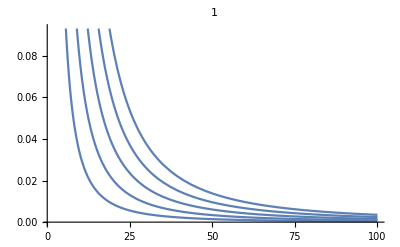
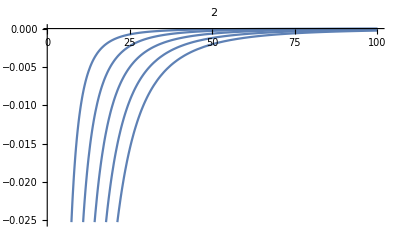
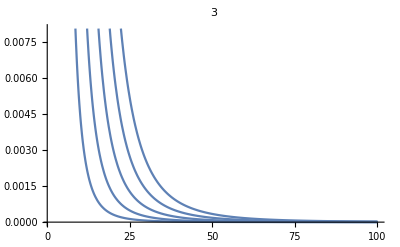

```mathematica
Table[
Plot[Table[(1.-(seriesElongPrX[x, order])/(ⅇ^x x ExpIntegralE[j,x])/.{y->1/x}), {j, 1.5, 5.5}], {x, 1, 100},
PlotLabel->order
], {order, 1, 3}]
```

```mathematica
Integrate[Exp[-x t]/t^n,{t, 0, ∞}]
```

ConditionalExpression[x^(-1+n) Gamma[1-n],Re[x]>0&&Re[n]<1]

```mathematica
Integrate[Exp[-x t]/t^n, {t, 0, 1}, Assumptions->{Element[n, Reals], n>1}]


(%-ExpIntegalE[n, x])/.{n->2, x->3.4}
```

Integrate::idiv: Integral of ⅇ^-t\ x\ t^-n does not converge on {0, 1}.

Integrate[ⅇ^(-t x) t^-n,{t,0,1},Assumptions→{n∈Reals,n>1}]

Integrate::idiv: Integral of ⅇ^-t\ x\ t^-n does not converge on {0, 1}.

Integrate::idiv: Integral of ⅇ^-3.4\ t/t^2 does not converge on {0, 1}.

-ExpIntegalE[2,3.4]+Integrate[ⅇ^(-3.4 t)/t^2,{t,0,1},Assumptions→{True,True}]

```mathematica
?ExpIntegralE
```

ExpIntegralE[n,z] gives the exponential integral function E_n(z).

```mathematica
Series[ⅇ^(lambda[j]/b) lambda[j]/b ExpIntegralE[alpha[j],lambda[j] 1/b] , {b, 0, 4}]
```

1-(alpha[j] b)/lambda[j]+((alpha[j]+alpha[j]^2) b^2)/lambda[j]^2-(alpha[j] (1+alpha[j]) (2+alpha[j]) b^3)/lambda[j]^3+(alpha[j] (1+alpha[j]) (2+alpha[j]) (3+alpha[j]) b^4)/lambda[j]^4+O[b]^5

```mathematica
Series[Exp[x], {x, 0, 4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
Product[Series[ⅇ^(lambda[j]/b) lambda[j]/b ExpIntegralE[alpha[j],lambda[j] 1/b] , {b, 0, 2}], {j,1, i}]
```

∏_(j=1)^i (1-(alpha[j] b)/lambda[j]+((alpha[j]+alpha[j]^2) b^2)/lambda[j]^2+O[b]^3)

```mathematica
(%/.{i->4})//Simplify
```

1+(-alpha[1]/lambda[1]-alpha[2]/lambda[2]-alpha[3]/lambda[3]-alpha[4]/lambda[4]) b+((alpha[1] (1+alpha[1]))/lambda[1]^2+(alpha[2] (1+alpha[2]))/lambda[2]^2+(alpha[1] alpha[2])/(lambda[1] lambda[2])+(alpha[3] (1+alpha[3]))/lambda[3]^2+(alpha[3] (alpha[2] lambda[1]+alpha[1] lambda[2]))/(lambda[1] lambda[2] lambda[3])+(alpha[4] (1+alpha[4]))/lambda[4]^2-(alpha[4] (-alpha[1]/lambda[1]-alpha[2]/lambda[2]-alpha[3]/lambda[3]))/lambda[4]) b^2+O[b]^3

```mathematica
1+(-alpha[1]/lambda[1]-alpha[2]/lambda[2]-alpha[3]/lambda[3]-alpha[4]/lambda[4]) b+((alpha[1] (1+alpha[1]))/lambda[1]^2+(alpha[2] (1+alpha[2]))/lambda[2]^2+(alpha[1] alpha[2])/(lambda[1] lambda[2])+(alpha[3] (1+alpha[3]))/lambda[3]^2+(alpha[3] (alpha[2] lambda[1]+alpha[1] lambda[2]))/(lambda[1] lambda[2] lambda[3])+(alpha[4] (1+alpha[4]))/lambda[4]^2-(alpha[4] (-alpha[1]/lambda[1]-alpha[2]/lambda[2]-alpha[3]/lambda[3]))/lambda[4]) b^2+O[b]^3

1-Sum[alpha[j]/lambda[j], {j, i}]
```

```mathematica
sigma[i]
```

∏_(j=1)^i ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]

```mathematica
C[1]
```

C[1]

```mathematica
newNseAssumptions = {w[i]>0, v[i] > 0,b[i] > 0, lambda[i]>0, alpha[i]>0, Y[i]≥0, C[1]>0}
```

{w[i]>0,v[i]>0,b[i]>0,lambda[i]>0,alpha[i]>0,Y[i]≥0,C[1]>0}

Integrate across uncertainty in w_i when calculating terms.  This should be a correct PDF for Y[i]

```mathematica
PDF[PoissonDistribution[C[1](w[i] v[i])/(w[i] + v[i])], Y[i]]

Simplify[%PDF[GammaDistribution[alpha[i], 1/lambda[i]], w[i]], Assumptions->{Y[i]≥0, w[i]>0}]
%//PowerExpand//Simplify

Limit[%, v[i]->0, Direction->-1]//Simplify
```

Piecewise[{{1/(Y[i]!)ⅇ^(-(C[1] v[i] w[i])/(v[i]+w[i])) ((C[1] v[i] w[i])/(v[i]+w[i]))^Y[i], Y[i]≥0}, {0, True}}]

(ⅇ^(-w[i] (lambda[i]+(C[1] v[i])/(v[i]+w[i]))) (1/lambda[i])^(-alpha[i]) w[i]^(-1+alpha[i]) ((C[1] v[i] w[i])/(v[i]+w[i]))^Y[i])/(Y[i]! Gamma[alpha[i]])

(ⅇ^(-w[i] (lambda[i]+(C[1] v[i])/(v[i]+w[i]))) C[1]^Y[i] lambda[i]^alpha[i] v[i]^Y[i] w[i]^(-1+alpha[i]+Y[i]) (v[i]+w[i])^(-Y[i]))/(Y[i]! Gamma[alpha[i]])

Limit[(ⅇ^(-w[i] (lambda[i]+(C[1] v[i])/(v[i]+w[i]))) C[1]^Y[i] lambda[i]^alpha[i] v[i]^Y[i] w[i]^(-1+alpha[i]+Y[i]) (v[i]+w[i])^(-Y[i]))/(Y[i]! Gamma[alpha[i]]),v[i]→0,Direction→-1]

```mathematica
?Limit
```

RowBox[{"Limit", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{StyleBox["x", "TI"], "→", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}]}], "]"}] finds the limiting value of StyleBox["expr", "TI"] when StyleBox["x", "TI"] approaches SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]].

```mathematica
Simplify[
Integrate[Simplify[Series[PDF[PoissonDistribution[C[1](w[i] v[i])/(w[i] + v[i])], Y[i]]/.{v[i]-> 1/b[i]}, {b[i], 0, 1}]PDF[GammaDistribution[alpha[i], 1/lambda[i]], w[i]],Assumptions->newNseAssumptions ], {w[i], 0, ∞}, Assumptions->newNseAssumptions]/.{b[i] ->1/v[i]}, Assumptions->newNseAssumptions]


Simplify[
Integrate[Simplify[(Series[PDF[PoissonDistribution[C[1](w[i] v[i])/(w[i] + v[i])], Y[i]]/.{v[i]-> 1/b[i]}, {b[i], 0, 1}]//Normal)PDF[GammaDistribution[alpha[i], 1/lambda[i]], w[i]],Assumptions->newNseAssumptions ], {w[i], 0, ∞}, Assumptions->newNseAssumptions]/.{b[i] ->1/v[i]}, Assumptions->newNseAssumptions]
```

SeriesData::sdatv: First argument 1/v[i] is not a valid variable.

Integrate[(ⅇ^(-(C[1]+lambda[i]) w[i]) C[1]^Y[i] lambda[i]^alpha[i] w[i]^(-1+alpha[i]+Y[i]))/(Y[i]! Gamma[alpha[i]])+(ⅇ^(-(C[1]+lambda[i]) w[i]) (C[1] w[i])^Y[i] (lambda[i] w[i])^alpha[i] (C[1] w[i]-Y[i]))/(Y[i]! Gamma[alpha[i]] v[i])+O[1/v[i]]^2,{w[i],0,∞},Assumptions→Y[i]≥0&&alpha[i]>0&&b[i]>0&&C[1]>0&&lambda[i]>0&&v[i]>0&&w[i]>0]

1/(Y[i]! Gamma[alpha[i]])C[1]^Y[i] Gamma[alpha[i]+Y[i]] lambda[i]^alpha[i] (C[1]+lambda[i])^(-2-alpha[i]-Y[i]) (C[1]^2+2 C[1] lambda[i]+lambda[i]^2+((1+alpha[i]) C[1] (alpha[i]+Y[i]))/v[i]-(lambda[i] Y[i] (alpha[i]+Y[i]))/v[i])

(C[1]^Y[i] Gamma[alpha[i]+Y[i]] lambda[i]^alpha[i])/(Y[i]! Gamma[alpha[i]]) (C[1]+lambda[i])^(-2-alpha[i]-Y[i]) (C[1]^2+2 C[1] lambda[i]+lambda[i]^2+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/v[i])

=(C[1]/(C[1]+lambda[i]))^Y[i](Gamma[alpha[i]+Y[i]] lambda[i]^alpha[i])/(Y[i]! Gamma[alpha[i]]) (C[1]+lambda[i])^(-2-alpha[i]) (C[1]^2+2 C[1] lambda[i]+lambda[i]^2+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/v[i])

=(C[1]/(C[1]+lambda[i]))^Y[i]Gamma[alpha[i]+Y[i]]/(Y[i]! Gamma[alpha[i]]) (lambda[i]/(C[1]+lambda[i]))^alpha[i](C[1]^2+2 C[1] lambda[i]+lambda[i]^2+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/v[i])/(C[1]+lambda[i])^2

=(C[1]/(C[1]+lambda[i]))^Y[i]Gamma[alpha[i]+Y[i]]/(Y[i]! Gamma[alpha[i]]) (lambda[i]/(C[1]+lambda[i]))^alpha[i](C[1]^2+2 C[1] lambda[i]+lambda[i]^2+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/v[i])/(C[1]^2+2 C[1]lambda[i] + lambda[i]^2)

=(C[1]/(C[1]+lambda[i]))^Y[i]Gamma[alpha[i]+Y[i]]/(Y[i]! Gamma[alpha[i]]) (lambda[i]/(C[1]+lambda[i]))^alpha[i](1+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/(v[i](C[1]^2+2 C[1]lambda[i] + lambda[i]^2)))
=(C[1]/(C[1]+lambda[i]))^Y[i]Gamma[alpha[i]+Y[i]]/(Y[i]! Gamma[alpha[i]]) (lambda[i]/(C[1]+lambda[i]))^alpha[i](1+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/(v[i](C[1]+lambda[i])^2))

```mathematica
?ExpIntegralE
```

ExpIntegralE[n,z] gives the exponential integral function E_n(z).

Probability function for footprint counts using first order approximation for probability of position occupancy around 1/v[i] = b[i] ~0 where C[1] =κ m σ(i-1) = κ m  ∏_(j=1)^(i-1) ⅇ^(λ[j] v[j]) ExpIntegralE[α[j],λ[j] v[j]] λ[j] v[j]

```mathematica
(C[1]/(C[1]+lambda[i]))^Y[i] Gamma[alpha[i]+Y[i]]/(Y[i]! Gamma[alpha[i]]) (lambda[i]/(C[1]+lambda[i]))^alpha[i](1+((alpha[i]+Y[i])((1+alpha[i])C[1]-lambda[i] Y[i] ))/(v[i](C[1]+lambda[i])^2))
```

1/(Y[i]! Gamma[alpha[i]])Kg^Y[i] Gamma[alpha[i]+Y[i]] lambda[i]^alpha[i] (∏_(j=1)^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j])^Y[i] (lambda[i]+Kg ∏_(j=1)^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j])^(-2-alpha[i]-Y[i]) (lambda[i]^2+2 Kg lambda[i] ∏_(j=1)^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]+Kg^2 (∏_(j=1)^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j])^2+1/v[i]Kg (1+alpha[i]) (∏_(j=1)^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]) (alpha[i]+Y[i])-(lambda[i] Y[i] (alpha[i]+Y[i]))/v[i])

```mathematica
Integrate[Simplify[(Series[PDF[PoissonDistribution[C[1](w[i] v[i])/(w[i] + v[i])], Y[i]], {v[i], 0, 2}])PDF[GammaDistribution[alpha[i], 1/lambda[i]], w[i]],Assumptions-> {w[i]>0, v[i] > 0,lambda[i]>0, alpha[i]>0, Y[i]≥0, C[1]>0}], {w[i], 0, ∞}, Assumptions-> {w[i]>0, v[i] > 0,lambda[i]>0, alpha[i]>0, Y[i]≥0}]

Integrate[Simplify[(Series[PDF[PoissonDistribution[C[1](w[i] v[i])/(w[i] + v[i])], Y[i]], {v[i], 0, 2}]//Normal)PDF[GammaDistribution[alpha[i], 1/lambda[i]], w[i]],Assumptions-> {w[i]>0, v[i] > 0,lambda[i]>0, alpha[i]>0, Y[i]≥0, C[1]>0}], {w[i], 0, ∞}, Assumptions-> {w[i]>0, v[i] > 0,lambda[i]>0, alpha[i]>0, Y[i]≥0}]
```

Piecewise[{{1/(2 (-2+alpha[i]) (-1+alpha[i]) Gamma[1+Y[i]])C[1]^Y[i] v[i]^Y[i] (4-6 alpha[i]+2 alpha[i]^2-4 C[1] v[i]+6 alpha[i] C[1] v[i]-2 alpha[i]^2 C[1] v[i]+2 C[1]^2 v[i]^2-3 alpha[i] C[1]^2 v[i]^2+alpha[i]^2 C[1]^2 v[i]^2-4 C[1] lambda[i] v[i]^2+2 alpha[i] C[1] lambda[i] v[i]^2+4 lambda[i] v[i] Y[i]-2 alpha[i] lambda[i] v[i] Y[i]-4 C[1] lambda[i] v[i]^2 Y[i]+2 alpha[i] C[1] lambda[i] v[i]^2 Y[i]+lambda[i]^2 v[i]^2 Y[i]+lambda[i]^2 v[i]^2 Y[i]^2), alpha[i]>2}, {Integrate[(Piecewise[{{(1/(Y[i]!)+((-C[1] w[i]-Y[i]) v[i])/(Y[i]! w[i])+((2 C[1] w[i]+C[1]^2 w[i]^2+Y[i]+2 C[1] w[i] Y[i]+Y[i]^2) v[i]^2)/(2 Y[i]! w[i]^2)+O[v[i]]^3) (C[1] v[i])^Y[i], Y[i]≥0}, {0, True}}]) (Piecewise[{{(ⅇ^(-lambda[i] w[i]) (1/lambda[i])^(-alpha[i]) w[i]^(-1+alpha[i]))/Gamma[alpha[i]], w[i]>0}, {0, True}}]),{w[i],0,∞},Assumptions→w[i]>0&&v[i]>0&&lambda[i]>0&&0<alpha[i]≤2&&Y[i]≥0], True}}]

ConditionalExpression[1/(2 Y[i]! Gamma[alpha[i]])Gamma[-2+alpha[i]] (C[1] v[i])^Y[i] ((-2+alpha[i]) (2 (-1+alpha[i])-2 (-1+alpha[i]) C[1] v[i]+C[1] ((-1+alpha[i]) C[1]+2 lambda[i]) v[i]^2)+lambda[i] v[i] (4-2 alpha[i]+(2 (-2+alpha[i]) C[1]+lambda[i]) v[i]) Y[i]+lambda[i]^2 v[i]^2 Y[i]^2),alpha[i]>2]

```mathematica
zhat[i]
```

(ⅇ^(-lambda[i] w[i]) Kg (1/lambda[i])^(-alpha[i]) sigma[-1+i] v[i] w[i]^alpha[i])/(Gamma[alpha[i]] (v[i]+w[i]))

```mathematica
?Conditioned
```

Conditioned[expr,cond] or expr\[Conditioned]cond represents expr conditioned by the predicate cond.

```mathematica
Simplify[zhat[i]/.{sigma[-1 +i]-> (Product[ ⅇ^(lambda[j] v[j]) lambda[j] v[j] ExpIntegralE[alpha[j],lambda[j] v[j]], {j, i-1}])}, Assumptions->w[i]>0]
```

(ⅇ^(-lambda[i] w[i]) Kg (1/lambda[i])^(-alpha[i]) (∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]) v[i] w[i]^alpha[i])/(Gamma[alpha[i]] (v[i]+w[i]))

```mathematica
Print["Gamma, Fixed"]
RFP["NSE Gamma, Fixed"] = FullSimplify[Integrate[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi] , {wgi, 0, ∞}, Assumptions ->nseAssumptions], Assumptions->nseAssumptions]


Print["InverseGamma, Fixed"]
RFP["NSE InverseGamma, Fixed"] = FullSimplify[Integrate[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] *PDF[InverseGammaDistribution[alpha, 1/lambda], wgi] ,{wgi, 0, ∞},Assumptions ->nseAssumptions], Assumptions->nseAssumptions]
```

Gamma, Fixed

Integrate[(ⅇ^(-wgi (lambda+(Kg sigma vgi)/(vgi+wgi))) lambda^alpha wgi^(-1+alpha) ((Kg sigma vgi wgi)/(vgi+wgi))^Ygi)/(Ygi! Gamma[alpha]),{wgi,0,∞},Assumptions→sigma<1&&Ygi≥0&&alpha>0&&beta>0&&Kg>0&&lambda>0&&mu>0&&sigma>0&&vgi>0&&wgi>0]

InverseGamma, Fixed

Integrate[(ⅇ^(-1/(lambda wgi)-(Kg sigma vgi wgi)/(vgi+wgi)) lambda (1/(lambda wgi))^(1+alpha) ((Kg sigma vgi wgi)/(vgi+wgi))^Ygi)/(Ygi! Gamma[alpha]),{wgi,0,∞},Assumptions→sigma<1&&Ygi≥0&&alpha>0&&beta>0&&Kg>0&&lambda>0&&mu>0&&sigma>0&&vgi>0&&wgi>0]

#### Taylor Series Approximation

```mathematica
Table[
tmp = Normal[Series[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] /.{vgi->1/bgi}, {bgi, 0, order}, Assumptions->nseAssumptions]]/.{bgi->1/vgi};

condPrYgi[order] = FullSimplify[tmp, Assumptions->nseAssumptions
], {order, 1, 3}]
```

{(ⅇ^(-Kg sigma wgi) (Kg sigma wgi)^Ygi (vgi+wgi (Kg sigma wgi-Ygi)))/(vgi Ygi!),1/(2 vgi^2 Ygi!)ⅇ^(-Kg sigma wgi) (Kg sigma wgi)^Ygi (2 vgi^2+2 vgi wgi (Kg sigma wgi-Ygi)+wgi^2 (Kg sigma wgi (-2+Kg sigma wgi)+Ygi-2 Kg sigma wgi Ygi+Ygi^2)),1/(6 vgi^3 Ygi!)ⅇ^(-Kg sigma wgi) (Kg sigma wgi)^Ygi (6 vgi^3+6 vgi^2 wgi (Kg sigma wgi-Ygi)+3 vgi wgi^2 (Kg sigma wgi (-2+Kg sigma wgi)+Ygi-2 Kg sigma wgi Ygi+Ygi^2)+wgi^3 (Kg^3 sigma^3 wgi^3-3 Kg^2 sigma^2 wgi^2 (2+Ygi)+3 Kg sigma wgi (1+Ygi) (2+Ygi)-Ygi (1+Ygi) (2+Ygi)))}

```mathematica
Table[
RFP[StringForm["NSE, Approx Order ``", order]//ToString]  = FullSimplify[
Integrate[condPrYgi[order]*PDF[GammaDistribution[alpha, 1/lambda], wgi], {wgi, 0, ∞}, 
Assumptions->nseAssumptions],Assumptions->nseAssumptions], {order, 1, 3}]
```

{1/(vgi Ygi! Gamma[alpha])lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-2-alpha-Ygi) (alpha^2 Kg sigma+(lambda+Kg sigma)^2 vgi+Kg sigma Ygi-lambda Ygi^2+alpha (-lambda Ygi+Kg sigma (1+Ygi))) Gamma[alpha+Ygi],(lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-4-alpha-Ygi) (alpha^4 Kg^2 sigma^2+2 (lambda+Kg sigma)^4 vgi^2+2 Kg sigma (-2 lambda+Kg sigma+(lambda+Kg sigma)^2 vgi) Ygi+(lambda^2-8 Kg lambda sigma+2 Kg^2 sigma^2-2 lambda (lambda+Kg sigma)^2 vgi) Ygi^2+2 lambda (lambda-2 Kg sigma) Ygi^3+lambda^2 Ygi^4+2 alpha^3 Kg sigma (-lambda (1+Ygi)+Kg sigma (2+Ygi))+alpha^2 (2 Kg^3 sigma^3 vgi+lambda^2 Ygi (1+Ygi)+Kg^2 sigma^2 (5+4 lambda vgi+Ygi (7+Ygi))+2 Kg lambda sigma (lambda vgi-(1+Ygi) (3+2 Ygi)))+alpha (2 Kg^3 sigma^3 vgi (1+Ygi)+Kg^2 sigma^2 (2+Ygi) (1+2 lambda vgi+3 Ygi)+lambda^2 Ygi (-2 lambda vgi+(1+Ygi) (1+2 Ygi))-2 Kg lambda sigma (lambda vgi (-1+Ygi)+(1+Ygi) (2+Ygi (5+Ygi))))) Gamma[alpha+Ygi])/(2 vgi^2 Ygi! Gamma[alpha]),(lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-6-alpha-Ygi) (6 (lambda+Kg sigma)^6 vgi^3-6 (lambda+Kg sigma)^5 vgi^2 Ygi (alpha+Ygi)-3 Kg^2 sigma^2 (lambda+Kg sigma) (2+Ygi) (alpha+Ygi) (1+alpha+Ygi) (2+alpha+Ygi) (3+alpha+Ygi) (4+alpha+Ygi)+Kg^3 sigma^3 (alpha+Ygi) (1+alpha+Ygi) (2+alpha+Ygi) (3+alpha+Ygi) (4+alpha+Ygi) (5+alpha+Ygi)+3 (lambda+Kg sigma)^4 vgi (alpha+Ygi) (1+alpha+Ygi) (2 Kg sigma vgi+Ygi+Ygi^2)-(lambda+Kg sigma)^3 (1+Ygi) (alpha+Ygi) (1+alpha+Ygi) (2+alpha+Ygi) (6 Kg sigma vgi+Ygi (2+Ygi))+3 Kg sigma (lambda+Kg sigma)^2 (alpha+Ygi) (1+alpha+Ygi) (2+alpha+Ygi) (3+alpha+Ygi) (Kg sigma vgi+(1+Ygi) (2+Ygi))) Gamma[alpha+Ygi])/(6 vgi^3 Ygi! Gamma[alpha])}

```mathematica
RFP["NSE, Approx Order 1"] = 1/(vgi Ygi! Gamma[alpha])lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-2-alpha-Ygi) (alpha^2 Kg sigma+(lambda+Kg sigma)^2 vgi+Kg sigma Ygi-lambda Ygi^2+alpha (-lambda Ygi+Kg sigma (1+Ygi))) Gamma[alpha+Ygi]
```

```mathematica
1/(vgi Ygi! Gamma[alpha])lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-2-alpha-Ygi) (alpha^2 Kg sigma+(lambda+Kg sigma)^2 vgi+Kg sigma Ygi-lambda Ygi^2+alpha (-lambda Ygi+Kg sigma (1+Ygi))) Gamma[alpha+Ygi]
```

```mathematica
RFP["NSE, Approx Order 1"]/.{lambda-> lambda[i], alpha-> alpha[i], Ygi->Y[i], vgi->v[i], wgi->w[i], sigma -> Product[ⅇ^(lambda[j] v[j]) lambda[j] v[j] ExpIntegralE[alpha[j],lambda[j] v[j]], {j, i-1}]}//Simplify

Series[%/.{i-> 4}, Sequence@@Table[{v[j], 0, 1}, {j, 3}] ]
```

1/(Y[i]! Gamma[alpha[i]] v[i])Gamma[alpha[i]+Y[i]] lambda[i]^alpha[i] (Kg ∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j])^Y[i] (lambda[i]+Kg ∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j])^(-2-alpha[i]-Y[i]) (Kg alpha[i]^2 ∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]+(lambda[i]+Kg ∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j])^2 v[i]+Kg (∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]) Y[i]-lambda[i] Y[i]^2+alpha[i] (-lambda[i] Y[i]+Kg (∏_j^(-1+i) ⅇ^(lambda[j] v[j]) ExpIntegralE[alpha[j],lambda[j] v[j]] lambda[j] v[j]) (1+Y[i])))

(((Gamma[alpha[4]+Y[4]] lambda[4]^(1+alpha[4]) (lambda[4] v[4]-alpha[4] Y[4]-Y[4]^2))/(Y[4]! Gamma[alpha[4]] v[4])+(((((Kg Gamma[alpha[4]+Y[4]] lambda[1] lambda[2] lambda[3] lambda[4]^alpha[4] (alpha[4]+alpha[4]^2+2 lambda[4] v[4]+Y[4]+alpha[4] Y[4]) v[3])/((-1+alpha[1]) (-1+alpha[2]) (-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) ((Kg Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1] lambda[2] lambda[3]^alpha[3] lambda[4]^alpha[4] (alpha[4]+alpha[4]^2+2 lambda[4] v[4]+Y[4]+alpha[4] Y[4]))/((-1+alpha[1]) (-1+alpha[2]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^1) v[3]^alpha[3]) v[2]+O[v[2]]^2)+ⅇ^(2 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) ((((Kg Gamma[1-alpha[2]] Gamma[alpha[4]+Y[4]] lambda[1] lambda[2]^alpha[2] lambda[3] lambda[4]^alpha[4] (alpha[4]+alpha[4]^2+2 lambda[4] v[4]+Y[4]+alpha[4] Y[4]) v[3])/((-1+alpha[1]) (-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) ((Kg Gamma[1-alpha[2]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1] lambda[2]^alpha[2] lambda[3]^alpha[3] lambda[4]^alpha[4] (alpha[4]+alpha[4]^2+2 lambda[4] v[4]+Y[4]+alpha[4] Y[4]))/((-1+alpha[1]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^1) v[3]^alpha[3])+O[v[2]]^1) v[2]^alpha[2]) v[1]+O[v[1]]^2)+ⅇ^(2 ⅈ π (-1+alpha[1]) Floor[(π-Arg[lambda[1]]-Arg[v[1]])/(2 π)]) ((((((2 Kg Gamma[1-alpha[1]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3] lambda[4]^(1+alpha[4]) v[3])/((-1+alpha[2]) (-1+alpha[3]) Y[4]! Gamma[alpha[4]])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) ((2 Kg Gamma[1-alpha[1]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3]^alpha[3] lambda[4]^(1+alpha[4]))/((-1+alpha[2]) Y[4]! Gamma[alpha[4]])+O[v[3]]^1) v[3]^alpha[3]) v[2]+O[v[2]]^2)+ⅇ^(2 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) ((((2 Kg Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3] lambda[4]^(1+alpha[4]) v[3])/((-1+alpha[3]) Y[4]! Gamma[alpha[4]])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) (1/(Y[4]! Gamma[alpha[4]])2 Kg Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3]^alpha[3] lambda[4]^(1+alpha[4])+O[v[3]]^1) v[3]^alpha[3])+O[v[2]]^1) v[2]^alpha[2])+O[v[1]]^1) v[1]^alpha[1]+ⅇ^(2 ⅈ π (-1+alpha[1]) Floor[(π-Arg[lambda[1]]-Arg[v[1]])/(2 π)]) ((((((Kg alpha[4]^2 Gamma[1-alpha[1]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3] lambda[4]^alpha[4] v[3])/((-1+alpha[2]) (-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) ((Kg alpha[4]^2 Gamma[1-alpha[1]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3]^alpha[3] lambda[4]^alpha[4])/((-1+alpha[2]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^1) v[3]^alpha[3]) v[2]+O[v[2]]^2)+ⅇ^(2 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) ((((Kg alpha[4]^2 Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3] lambda[4]^alpha[4] v[3])/((-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) (1/(Y[4]! Gamma[alpha[4]] v[4])Kg alpha[4]^2 Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3]^alpha[3] lambda[4]^alpha[4]+O[v[3]]^1) v[3]^alpha[3])+O[v[2]]^1) v[2]^alpha[2])+O[v[1]]^1) v[1]^alpha[1]+ⅇ^(2 ⅈ π (-1+alpha[1]) Floor[(π-Arg[lambda[1]]-Arg[v[1]])/(2 π)]) ((((((Kg Gamma[1-alpha[1]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3] lambda[4]^alpha[4] Y[4] v[3])/((-1+alpha[2]) (-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) ((Kg Gamma[1-alpha[1]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3]^alpha[3] lambda[4]^alpha[4] Y[4])/((-1+alpha[2]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^1) v[3]^alpha[3]) v[2]+O[v[2]]^2)+ⅇ^(2 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) ((((Kg Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3] lambda[4]^alpha[4] Y[4] v[3])/((-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) (1/(Y[4]! Gamma[alpha[4]] v[4])Kg Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3]^alpha[3] lambda[4]^alpha[4] Y[4]+O[v[3]]^1) v[3]^alpha[3])+O[v[2]]^1) v[2]^alpha[2])+O[v[1]]^1) v[1]^alpha[1]+ⅇ^(2 ⅈ π (-1+alpha[1]) Floor[(π-Arg[lambda[1]]-Arg[v[1]])/(2 π)]) ((((((Kg alpha[4] Gamma[1-alpha[1]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3] lambda[4]^alpha[4] (1+Y[4]) v[3])/((-1+alpha[2]) (-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) ((Kg alpha[4] Gamma[1-alpha[1]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2] lambda[3]^alpha[3] lambda[4]^alpha[4] (1+Y[4]))/((-1+alpha[2]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^1) v[3]^alpha[3]) v[2]+O[v[2]]^2)+ⅇ^(2 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) ((((Kg alpha[4] Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3] lambda[4]^alpha[4] (1+Y[4]) v[3])/((-1+alpha[3]) Y[4]! Gamma[alpha[4]] v[4])+O[v[3]]^2)+ⅇ^(2 ⅈ π (-1+alpha[3]) Floor[(π-Arg[lambda[3]]-Arg[v[3]])/(2 π)]) (1/(Y[4]! Gamma[alpha[4]] v[4])Kg alpha[4] Gamma[1-alpha[1]] Gamma[1-alpha[2]] Gamma[1-alpha[3]] Gamma[alpha[4]+Y[4]] lambda[1]^alpha[1] lambda[2]^alpha[2] lambda[3]^alpha[3] lambda[4]^alpha[4] (1+Y[4])+O[v[3]]^1) v[3]^alpha[3])+O[v[2]]^1) v[2]^alpha[2])+O[v[1]]^1) v[1]^alpha[1]+ⅇ^(4 ⅈ π (-1+alpha[1]) Floor[(π-Arg[lambda[1]]-Arg[v[1]])/(2 π)]) ((O[v[2]]^2+ⅇ^(2 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) O[v[2]]^1 v[2]^alpha[2]+ⅇ^(4 ⅈ π (-1+alpha[2]) Floor[(π-Arg[lambda[2]]-Arg[v[2]])/(2 π)]) O[v[2]]^0 v[2]^(2 alpha[2]))+O[v[1]]^1) v[1]^(2 alpha[1])) (ⅇ^(lambda[1] v[1]+lambda[2] v[2]+lambda[3] v[3]) Kg ExpIntegralE[alpha[1],lambda[1] v[1]] ExpIntegralE[alpha[2],lambda[2] v[2]] ExpIntegralE[alpha[3],lambda[3] v[3]] lambda[1] lambda[2] lambda[3] v[1] v[2] v[3])^Y[4] (lambda[4]+ⅇ^(lambda[1] v[1]+lambda[2] v[2]+lambda[3] v[3]) Kg ExpIntegralE[alpha[1],lambda[1] v[1]] ExpIntegralE[alpha[2],lambda[2] v[2]] ExpIntegralE[alpha[3],lambda[3] v[3]] lambda[1] lambda[2] lambda[3] v[1] v[2] v[3])^(-2-alpha[4]-Y[4])

```mathematica
RFP["NSE, Approx Order 1"]
RFP["ROC"]

%%/%//FullSimplify

Log[%//PowerExpand]
```

1/(vgi Ygi! Gamma[alpha])lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-2-alpha-Ygi) (alpha^2 Kg sigma+(lambda+Kg sigma)^2 vgi+Kg sigma Ygi-lambda Ygi^2+alpha (-lambda Ygi+Kg sigma (1+Ygi))) Gamma[alpha+Ygi]

(Kg^Ygi lambda^alpha (Kg+lambda)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Ygi! Gamma[alpha])

1/vgi Kg^-Ygi (Kg+lambda)^(alpha+Ygi) (Kg sigma)^Ygi (lambda+Kg sigma)^(-2-alpha-Ygi) (alpha^2 Kg sigma+(lambda+Kg sigma)^2 vgi+Kg sigma Ygi-lambda Ygi^2+alpha (-lambda Ygi+Kg sigma (1+Ygi)))

Log[1/vgi(Kg+lambda)^(alpha+Ygi) sigma^Ygi (lambda+Kg sigma)^(-2-alpha-Ygi) (alpha^2 Kg sigma+(lambda+Kg sigma)^2 vgi+Kg sigma Ygi-lambda Ygi^2+alpha (-lambda Ygi+Kg sigma (1+Ygi)))]

```mathematica
RFP["NSE, Approx Order 1"]
```

RFP[NSE, Approx Order 1]

Keep Taylor Series higher order term notations.  THe end results seem equivalent to the ROC model which is unexpected.

```mathematica
Clear[tmp]
Table[
tmp = Series[PDF[PoissonDistribution[ Kg sigma (vgi wgi)/(vgi+wgi)], Ygi] /.{vgi->1/bgi}, {bgi, 0, order}, Assumptions->nseAssumptions];

condPrYgiII[order] = FullSimplify[tmp//Normal, Assumptions->nseAssumptions
], {order, 1, 3}]
```

{(ⅇ^(-Kg sigma wgi) (Kg sigma wgi)^Ygi)/(Ygi!)+(ⅇ^(-Kg sigma wgi) wgi (Kg sigma wgi)^Ygi (Kg sigma wgi-Ygi) bgi)/(Ygi!)+O[bgi]^2,(ⅇ^(-Kg sigma wgi) (Kg sigma wgi)^Ygi)/(Ygi!)+(ⅇ^(-Kg sigma wgi) wgi (Kg sigma wgi)^Ygi (Kg sigma wgi-Ygi) bgi)/(Ygi!)+1/(2 Ygi!)ⅇ^(-Kg sigma wgi) wgi^2 (Kg sigma wgi)^Ygi (Kg sigma wgi (-2+Kg sigma wgi)+Ygi-2 Kg sigma wgi Ygi+Ygi^2) bgi^2+O[bgi]^3,(ⅇ^(-Kg sigma wgi) (Kg sigma wgi)^Ygi)/(Ygi!)+(ⅇ^(-Kg sigma wgi) wgi (Kg sigma wgi)^Ygi (Kg sigma wgi-Ygi) bgi)/(Ygi!)+1/(2 Ygi!)ⅇ^(-Kg sigma wgi) wgi^2 (Kg sigma wgi)^Ygi (Kg sigma wgi (-2+Kg sigma wgi)+Ygi-2 Kg sigma wgi Ygi+Ygi^2) bgi^2+1/(6 Ygi!)ⅇ^(-Kg sigma wgi) wgi^3 (Kg sigma wgi)^Ygi (Kg^3 sigma^3 wgi^3-3 Kg^2 sigma^2 wgi^2 (2+Ygi)+3 Kg sigma wgi (1+Ygi) (2+Ygi)-Ygi (1+Ygi) (2+Ygi)) bgi^3+O[bgi]^4}

```mathematica
Table[
RFP[StringForm["NSE, Approx Order `` II", order]//ToString]  = FullSimplify[
Integrate[condPrYgiII[order]*PDF[GammaDistribution[alpha, 1/lambda], wgi], {wgi, 0, ∞}, 
Assumptions->nseAssumptions],Assumptions->nseAssumptions], {order, 1, 3}]
```

{(lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Gamma[alpha] Gamma[1+Ygi]),(lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Gamma[alpha] Gamma[1+Ygi]),(lambda^alpha (Kg sigma)^Ygi (lambda+Kg sigma)^(-alpha-Ygi) Gamma[alpha+Ygi])/(Gamma[alpha] Gamma[1+Ygi])}

#### Explicitly combining σ and Expected Counts

```mathematica
prElong["Gamma, Fixed"]= ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi]/.{vgi->1/bgi}

σ[i_]:= prElong["Gamma, Fixed"]^i
```

(ⅇ^(lambda/bgi) lambda ExpIntegralE[alpha,lambda/bgi])/bgi

```mathematica
tmp[∞] =Simplify[ 
PDF[PoissonDistribution[ Kg( (ⅇ^(lambda/bgi) lambda ExpIntegralE[alpha,lambda/bgi])/bgi)^(i-1) (wgi/bgi)/(1+wgi/bgi)], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi], Assumptions->Join[{i > 1, Element[i, Integers]}, nseAssumptions
]
];

tmpInt[∞] = Integrate[tmp[∞], {wgi, 0, ∞}, Assumptions->Join[{i > 1, Element[i, Integers], Element[alpha, Reals]}, nseAssumptions]];
```

```mathematica
FullSimplify[tmp[∞]/.{bgi->1/vgi}, Assumptions->Join[{i > 1, Element[i, Integers], Element[alpha, Reals]}, nseAssumptions]]

FullSimplify[tmpInt[∞]/.{bgi->1/vgi}, Assumptions->Join[{i > 1, Element[i, Integers], Element[alpha, Reals]}, nseAssumptions]]
```

1/(Ygi! Gamma[alpha])ⅇ^(-wgi (lambda+(Kg vgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1+vgi wgi))) lambda^alpha wgi^(-1+alpha) ((Kg wgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1/vgi+wgi))^Ygi

Integrate[1/(Ygi! Gamma[alpha])ⅇ^(-wgi (lambda+(Kg vgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1+vgi wgi))) lambda^alpha wgi^(-1+alpha) ((Kg wgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1/vgi+wgi))^Ygi,{wgi,0,∞},Assumptions→i>1&&Ygi≥0&&wgi>0&&lambda>0&&alpha>0&&Kg>0&&sigma>0&&vgi>0&&beta>0&&mu>0&&bgi>0&&i∈Integers&&sigma<1]

```mathematica
Subscript[p, g,i]| wgi = 1/(Ygi! Gamma[alpha])ⅇ^(-wgi (lambda+(Kg vgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1+vgi wgi))) lambda^alpha wgi^(-1+alpha) ((Kg wgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1/vgi+wgi))^Ygi
		= 1/(Ygi! Gamma[alpha])ⅇ^(-wgi (lambda+(Kg vgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1+vgi wgi))) (lambda wgi)^alpha wgi^-1 ((Kg vgi wgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1+vgi wgi))^Ygi
		=  1/(Ygi! Gamma[alpha] wgi)ⅇ^(-wgi (lambda+(Kg vgi (ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(-1+i))/(1+vgi wgi))) (lambda wgi)^alpha  ((Kg vgi wgi)/(1+vgi wgi))^Ygi(ⅇ^(lambda vgi) lambda vgi ExpIntegralE[alpha,lambda vgi])^(Ygi(-1+i))
```

```mathematica
Series[tmp[∞], {bgi, 0, 1}]
Series[tmp[∞], {bgi, 0, 2}]//Simplify
```

(ⅇ^(-Kg-lambda wgi) Kg^Ygi lambda^alpha wgi^(-1+alpha))/(Ygi! Gamma[alpha])+(ⅇ^(-Kg-lambda wgi) Kg^Ygi lambda^(-1+alpha) wgi^(-2+alpha) (lambda-alpha wgi+alpha i wgi) (Kg-Ygi) bgi)/(Ygi! Gamma[alpha])+O[bgi]^2

(ⅇ^(-Kg-lambda wgi) Kg^Ygi lambda^alpha wgi^(-1+alpha))/(Ygi! Gamma[alpha])+(ⅇ^(-Kg-lambda wgi) Kg^Ygi lambda^(-1+alpha) wgi^(-2+alpha) (lambda+alpha (-1+i) wgi) (Kg-Ygi) bgi)/(Ygi! Gamma[alpha])+1/(2 Ygi! Gamma[alpha])ⅇ^(-Kg-lambda wgi) Kg^Ygi lambda^(-2+alpha) wgi^(-3+alpha) (Kg^2 (lambda+alpha (-1+i) wgi)^2+Ygi (2 alpha (-1+i) lambda wgi Ygi+lambda^2 (1+Ygi)+alpha (-1+i) wgi^2 (2+alpha (1+(-1+i) Ygi)))-Kg (2 lambda^2 (1+Ygi)+2 alpha (-1+i) lambda wgi (1+2 Ygi)+alpha (-1+i) wgi^2 (2+alpha (i-2 Ygi+2 i Ygi)))) bgi^2+O[bgi]^3

```mathematica
Integrate[Series[tmp[∞], {bgi, 0, 1}]//Normal, {wgi, 0, ∞}]
Integrate[Series[tmp[∞], {bgi, 0, 2}]//Normal, {wgi, 0, ∞}]
```

ConditionalExpression[(ⅇ^-Kg Kg^Ygi ((-1+alpha) lambda+(-1+alpha) alpha bgi (-1+i) (Kg-Ygi)+bgi lambda^2 (Kg-Ygi)) Gamma[-1+alpha])/(lambda Ygi! Gamma[alpha]),Re[lambda]>0&&Re[alpha]>1]

ConditionalExpression[1/(2 lambda^2 Ygi! Gamma[alpha])ⅇ^-Kg Kg^Ygi ((-2+alpha) (-1+alpha) alpha^2 bgi^2 (-1+i)^2 Kg^2+2 (-2+alpha) (-1+alpha) lambda^2+2 (-2+alpha) alpha bgi^2 (-1+i) Kg^2 lambda^2+bgi^2 Kg^2 lambda^4+2 (-2+alpha) (-1+alpha) alpha bgi (-1+i) lambda (Kg-Ygi)+2 (-2+alpha) bgi lambda^3 (Kg-Ygi)+2 (-2+alpha) alpha bgi^2 (-1+i) lambda^2 Ygi^2-2 bgi^2 Kg lambda^4 (1+Ygi)+bgi^2 lambda^4 Ygi (1+Ygi)-2 (-2+alpha) alpha bgi^2 (-1+i) Kg lambda^2 (1+2 Ygi)+(-2+alpha) (-1+alpha) alpha bgi^2 (-1+i) Ygi (2+alpha (1+(-1+i) Ygi))-(-2+alpha) (-1+alpha) alpha bgi^2 (-1+i) Kg (2+alpha (i-2 Ygi+2 i Ygi))) Gamma[-2+alpha],Re[lambda]>0&&Re[alpha]>2]

```mathematica
Clear[ i, j]

orderMax = 1;

Table[
tmp[order] = Series[PDF[PoissonDistribution[ Kg( (ⅇ^(lambda/bgi) lambda ExpIntegralE[alpha,lambda/bgi])/bgi)^(i-1) (wgi/bgi)/(1+wgi/bgi)], Ygi] *PDF[GammaDistribution[alpha, 1/lambda], wgi], {bgi, 0, order}, Assumptions->Join[{i > 1, Element[i, Integers]},nseAssumptions]
];
tmpInt[order] = Integrate[tmp[order]//Normal, {wgi, 0, ∞}, Assumptions->Join[{i > 1, Element[i, Integers], Element[alpha, Reals]},nseAssumptions]];,{order, orderMax}];

Table[tmp[order], {order, orderMax}]

Table[tmpInt[order], {order, orderMax}]
```

{ⅇ^(ⅇ^(lambda/bgi+((-1+i) lambda)/bgi) (lambda/bgi)^i ExpIntegralE[alpha,lambda/bgi]^i (-Kg+O[bgi]^1)+((lambda (-Ygi+i Ygi))/bgi-lambda wgi+O[bgi]^1)) (lambda/bgi)^((-1+i) Ygi) (ExpIntegralE[alpha,lambda/bgi]^(-1+i))^Ygi ((Kg^Ygi lambda^alpha wgi^(-1+alpha))/(Ygi! Gamma[alpha])-(Kg^Ygi lambda^alpha wgi^(-2+alpha) Ygi bgi)/(Ygi! Gamma[alpha])+O[bgi]^2)}

{ConditionalExpression[1/(Ygi! Gamma[alpha])ⅇ^(((-1+i) lambda Ygi)/bgi-ⅇ^((i lambda)/bgi) Kg ((lambda ExpIntegralE[alpha,lambda/bgi])/bgi)^i) (lambda/bgi)^((-1+i) Ygi) (-1+alpha-bgi lambda Ygi) (Kg ExpIntegralE[alpha,lambda/bgi]^(-1+i))^Ygi Gamma[-1+alpha],alpha>1]}

{ⅇ^(ⅇ^(lambda/bgi+((-1+i) lambda)/bgi) (lambda/bgi)^i ExpIntegralE[alpha,lambda/bgi]^i (-Kg+O[bgi]^1)+((lambda (-Ygi+i Ygi))/bgi-lambda wgi+O[bgi]^1)) (lambda/bgi)^((-1+i) Ygi) (ExpIntegralE[alpha,lambda/bgi]^(-1+i))^Ygi ((Kg^Ygi lambda^alpha wgi^(-1+alpha))/(Ygi! Gamma[alpha])-(Kg^Ygi lambda^alpha wgi^(-2+alpha) Ygi bgi)/(Ygi! Gamma[alpha])+O[bgi]^2),ⅇ^(ⅇ^(lambda/bgi+((-1+i) lambda)/bgi) (lambda/bgi)^i ExpIntegralE[alpha,lambda/bgi]^i (-Kg+(-(alpha Kg)/lambda+Kg/wgi) bgi+O[bgi]^2)+((lambda (-Ygi+i Ygi))/bgi-lambda wgi+O[bgi]^2)) (lambda/bgi)^((-1+i) Ygi) (ExpIntegralE[alpha,lambda/bgi]^(-1+i))^Ygi ((Kg^Ygi lambda^alpha wgi^(-1+alpha))/(Ygi! Gamma[alpha])-(Kg^Ygi lambda^alpha wgi^(-2+alpha) Ygi bgi)/(Ygi! Gamma[alpha])+(Kg^Ygi lambda^alpha wgi^(-3+alpha) Ygi (1+Ygi) bgi^2)/(2 Ygi! Gamma[alpha])+O[bgi]^3),tmp[3]}

{ConditionalExpression[1/(Ygi! Gamma[alpha])ⅇ^(((-1+i) lambda Ygi)/bgi-ⅇ^((i lambda)/bgi) Kg ((lambda ExpIntegralE[alpha,lambda/bgi])/bgi)^i) (lambda/bgi)^((-1+i) Ygi) (-1+alpha-bgi lambda Ygi) (Kg ExpIntegralE[alpha,lambda/bgi]^(-1+i))^Ygi Gamma[-1+alpha],alpha>1],ConditionalExpression[-1/(Kg Ygi! Gamma[alpha])bgi^(-alpha (-1/2+i)) ⅇ^((lambda (-2 Ygi+i (-3+alpha+2 Ygi)))/(2 bgi)-ⅇ^((i lambda)/bgi) Kg ((lambda ExpIntegralE[alpha,lambda/bgi])/bgi)^i-(alpha bgi ⅇ^((i lambda)/bgi) Kg ((lambda ExpIntegralE[alpha,lambda/bgi])/bgi)^i)/lambda) lambda^(-1+alpha) (lambda/bgi)^((-1+i) Ygi) (Kg ExpIntegralE[alpha,lambda/bgi]^(-1+i))^Ygi (-(lambda (lambda ExpIntegralE[alpha,lambda/bgi])^-i)/Kg)^(1-alpha/2) (-bgi^(1/2 (1+alpha) i) Ygi BesselK[1-alpha,2/(√(-(bgi^(-1+i) ⅇ^(-(i lambda)/bgi) (lambda ExpIntegralE[alpha,lambda/bgi])^-i)/(Kg lambda)))] √(-bgi Kg lambda (lambda ExpIntegralE[alpha,lambda/bgi])^-i) (-(-1+alpha) bgi^i (1+Ygi)+2 ⅇ^((i lambda)/bgi) Kg (lambda ExpIntegralE[alpha,lambda/bgi])^i)+bgi^((alpha i)/2) ⅇ^((i lambda)/(2 bgi)) Kg BesselK[-alpha,2/(√(-(bgi^(-1+i) ⅇ^(-(i lambda)/bgi) (lambda ExpIntegralE[alpha,lambda/bgi])^-i)/(Kg lambda)))] (-bgi^(1+i) lambda Ygi (1+Ygi)+2 ⅇ^((i lambda)/bgi) Kg (lambda ExpIntegralE[alpha,lambda/bgi])^i)),Re[ExpIntegralE[alpha,lambda/bgi]^i]<0],tmpInt[3]}

```mathematica
nseAssumptions
```

{Ygi≥0,wgi>0,lambda>0,alpha>0,Kg>0,sigma>0,sigma<1,vgi>0,beta>0,mu>0}

## Old

#### Old--Calculate Pr(Elongation) -used Pr(NSE) = vgi/(vgi+wgi)instead of (1/vgi)/(1/vgi+1/wgi) = wgi/(wgi+vgi)

Integrate over uncertainty to get terms needed for σ_i (pr reaching and translating codon i).

Note that a ‘moments’ approach would use something like Pr(NSE) =(β μ)/(β μ + α λ) but comparison to the exact solution suggests this is a poor approximation.

```mathematica
Print["wgi ~ Gamma, vgi ~ Gamma"]
prElongIntegrate = Integrate[ (1-vgi/(vgi+ wgi)) * PDF[GammaDistribution[alpha, 1/lambda], wgi] *PDF[GammaDistribution[beta, 1/mu], vgi], {wgi, 0, ∞}, {vgi, 0, ∞},
Assumptions ->{wgi>0, vgi>0, lambda>0, alpha>0, beta>0, mu>0}]//Simplify
```

wgi ~ Gamma, vgi ~ Gamma

alpha Gamma[alpha+beta] Hypergeometric2F1Regularized[1,beta,1+alpha+beta,1-lambda/mu]

According to Butler and Wood (2002), _2 F_1(a,b;c;z) = (Beta(a, c-a))^-1(∫_0)^1(y^(a-1)(1-y))^(c-a-1)(1-z y)^-b ⅆy
Thus,
	alpha Gamma[alpha+beta] Hypergeometric2F1Regularized[1,beta,1+alpha+beta,1-lambda/mu]
= alpha Gamma[alpha + beta] Hypergeometric2F1[1,beta,1+alpha+beta,1-lambda/mu]/Gamma[1+alpha+beta]
= alpha Gamma[alpha + beta]/Gamma[1+alpha+beta]((Gamma[1] Gamma[alpha+beta])/Gamma[1+alpha + beta])^-1(∫_0)^1(y^0(1-y))^(alpha+beta-1)(1-(1-lambda/mu)y)^-beta ⅆy
= alpha Gamma[alpha + beta]/Gamma[1+alpha+beta](Gamma[1+alpha + beta]/Gamma[alpha+beta])(∫_0)^1(1-y)^(alpha+beta-1)(1-y+lambda/mu y)^-beta ⅆy
  = alpha (∫_0)^1(1-y)^(alpha+beta-1)(1-y+lambda/mu y)^-beta ⅆy

```mathematica
alpha Integrate[(1-y)^(alpha+beta-1)(1-y+lambda/mu y)^-beta, {y, 0, 1}, Assumptions -> {lambda>0, beta>0, alpha>0, mu>0}]//FullSimplify
```

ConditionalExpression[(lambda^alpha (lambda-mu)^(-alpha-beta) (mu^beta π Csc[(alpha+beta) π] Gamma[1-beta]-alpha lambda^beta (mu/lambda)^beta Beta[mu/lambda,1-beta,alpha+beta] Gamma[alpha] Gamma[1-alpha-beta]))/(Gamma[alpha] Gamma[1-alpha-beta]),lambda≥mu]

```mathematica
prElongApprox = (alpha lambda)/(beta mu + alpha lambda)
```

(alpha lambda)/(alpha lambda+beta mu)

```mathematica
?TrueQ
```

TrueQ[expr] yields True if expr is True, and yields False otherwise.

```mathematica
?RandomReal
```

RandomReal[] gives a pseudorandom real number in the range 0 to 1. 
RandomReal[{x_min,x_max}] gives a pseudorandom real number in the range x_min to x_max. 
RandomReal[x_max] gives a pseudorandom real number in the range 0 to x_max.
RandomReal[range,n] gives a list of n pseudorandom reals. 
RandomReal[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom reals.

```mathematica
Block[{alpha, beta, mu, lambda, x, y},
Table[
{alpha, beta, mu, lambda} = RandomReal[{0, 10}, 4];
x = prElongApprox;
y = prElongIntegrate;
{alpha, beta, mu, lambda, y,x,  (y-x)/y}//N, {i, 10}
]
]

Block[{alpha, beta, mu, lambda, x, y},
Table[
{alpha, beta, mu, lambda} = RandomReal[{0, 10}, 4];
 prElongIntegrate//N, {i, 100}
]//Timing
]
```

{{3.11277,7.51611,4.44756,1.67384,0.500374,0.134847,0.730509},{0.689771,8.05279,8.65146,9.97942,0.0700326,0.0899195,-0.283967},{8.21353,5.39719,6.77744,9.69179,0.521806,0.685159,-0.313053},{4.63296,4.26299,2.52712,5.19832,0.362156,0.690932,-0.907832},{0.487061,6.0404,3.68016,6.08931,0.0490984,0.117714,-1.39752},{8.47216,8.5758,9.47235,9.39678,0.498852,0.494958,0.00780515},{8.08372,2.00975,0.672281,4.75108,0.419641,0.966016,-1.30201},{4.01816,8.09611,8.14501,7.13627,0.359255,0.303059,0.156425},{2.66482,3.19276,0.466275,6.37651,0.0753874,0.919446,-11.1963},{6.2659,1.45274,0.157671,0.498125,0.61644,0.931631,-0.511308}}

{0.03636,{0.173362,0.775279,0.807222,0.495743,0.226111,0.253369,0.204702,0.471002,0.721458,0.655273,0.424498,0.327007,0.00631427,0.398231,0.927682,0.0419658,0.644775,0.77635,0.366113,0.0487802,0.0279155,0.197987,0.891295,0.279375,0.508648,0.634408,0.985573,0.919521,0.955891,0.779397,0.437709,0.950199,0.904243,0.944714,0.689688,0.32514,0.554318,0.510634,0.775751,0.992129,0.167979,0.23853,0.0119281,0.893555,0.937322,0.00704657,0.647176,0.326865,0.51663,0.277991,0.461076,0.0201388,0.636006,0.217417,0.0103276,0.0458583,0.439298,0.636472,0.119456,0.730069,0.43456,0.0678147,0.163494,0.459668,0.305969,0.520312,0.724036,0.434633,0.511265,0.697736,0.271716,0.965053,0.966611,0.847196,0.208474,0.0697826,0.0916878,0.437653,0.330515,0.896911,0.175672,0.632202,0.707294,0.896967,0.535398,0.230026,0.461128,0.383478,0.217088,0.221263,0.641844,0.860396,0.950191,0.483741,0.0228867,0.592005,0.839885,0.193511,0.340175,0.966571}}

```mathematica
prElong =(1- 1/mu beta lambda Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu])
```

1-1/mu beta lambda Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu]

```mathematica
FullSimplify[prElong, Assumptions->{wgi>0, vgi>0, lambda>0, alpha>0, beta>0, mu>0}]
```

1-1/mu beta lambda Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu]

```mathematica
prElong^2//FullSimplify
```

(-1+1/mu beta lambda Gamma[alpha+beta] Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu])^2

```mathematica
?Hypergeometric2F1Regularized
```

Hypergeometric2F1Regularized[a,b,c,z] is the regularized hypergeometric function _2 F_1(a,b;c;z)/Γ(c).

Let gamma = beta mu

```mathematica
Series[(Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu]/.{beta->gamma/mu}), {gamma, 0, 2},Assumptions->{wgi>0, vgi>0, lambda>0, alpha>0, beta>0, mu>0}]//FullSimplify
```

Hypergeometric2F1Regularized[1,1,1+alpha,1-lambda/mu]+1/mu(Hypergeometric2F1Regularized^(0,0,1,0)[1,1,1+alpha,1-lambda/mu]+Hypergeometric2F1Regularized^(0,1,0,0)[1,1,1+alpha,1-lambda/mu]) gamma+1/(2 mu^2)(Hypergeometric2F1Regularized^(0,0,2,0)[1,1,1+alpha,1-lambda/mu]+2 Hypergeometric2F1Regularized^(0,1,1,0)[1,1,1+alpha,1-lambda/mu]+Hypergeometric2F1Regularized^(0,2,0,0)[1,1,1+alpha,1-lambda/mu]) gamma^2+O[gamma]^3

```mathematica
Limit[Hypergeometric2F1Regularized[1,1+beta,1+alpha+beta,1-lambda/mu]/.{beta->gamma/mu}, gamma->0, Direction->-1, Assumptions->{wgi>0, vgi>0, lambda>0, alpha>0, beta>0, mu>0}]
```

Hypergeometric2F1[1,1,1+alpha,1-lambda/mu]/Gamma[1+alpha]